## General setup

### Metric setup

#### Load up Steve’s GR & tensor libraries

```mathematica
SetDirectory[NotebookDirectory[]];
<<GRtensors
```

#### Set the metric for the example from Section 4.1. of Chesler & Yaffe’s review 1309.1439

```mathematica
ggValues={{-2A[t,r],0,0,0,1},{0,Σ[t,r]^2*Exp[B[t,r]],0,0,0},{0,0,Σ[t,r]^2*Exp[B[t,r]],0,0},{0,0,0,Σ[t,r]^2*Exp[-2B[t,r]],0},{1,0,0,0,0}};
ggiValues=Inverse[ggValues];
SetXMet[{t,x1,x2,x3,r},ggValues,ggiValues];
DisplayTensor[gg]//MatrixForm
```

gg[{DownVector,DownVector}] has components

(-2 A[t,r] | 0 | 0 | 0 | 1
0 | ⅇ^B[t,r] Σ[t,r]^2 | 0 | 0 | 0
0 | 0 | ⅇ^B[t,r] Σ[t,r]^2 | 0 | 0
0 | 0 | 0 | ⅇ^(-2 B[t,r]) Σ[t,r]^2 | 0
1 | 0 | 0 | 0 | 0)

#### Generate all the relevant GR tensors

```mathematica
NewTensor[chris, chrisDef, Simplify];
NewTensor[chrisCont,chrisContDef, Simplify];
NewTensor[ricci,QuickRicciDef, Simplify];
NewTensor[einstein,einsteinDef, Simplify];
NewTensor[riemann,riemannDef, Simplify];
scalarR = Simplify[ComputeScalarR];
```

#### Check that Ricci and Riemann are well defined

```mathematica
EinsteinCheckDef[DefaultIndexType]={DownVector,DownVector};
EinsteinCheckDef[{m_,n_}]:=ricci[{{m,DownVector},{n,DownVector}}]-1/2*gg[{{m,DownVector},{n,DownVector}}]*scalarR;
NewTensor[EinsteinCheck,EinsteinCheckDef,Simplify]
DisplayTensor[EinsteinCheck]-DisplayTensor[einstein]//Simplify
```

EinsteinCheck[{DownVector,DownVector}] has components

einstein[{DownVector,DownVector}] has components

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Raise[riemann,{UpVector,DownVector,DownVector,DownVector}];
RicciCheckDef[DefaultIndexType]={DownVector,DownVector};
RicciCheckDef[{μ_,κ_}]:=Sum[riemann[{{λ,UpVector},{μ,DownVector},{λ,DownVector},{κ,DownVector}}],{λ,1,dim}];
NewTensor[RicciCheck,RicciCheckDef,Simplify]
DisplayTensor[RicciCheck]-DisplayTensor[ricci]//Simplify
```

RicciCheck[{DownVector,DownVector}] has components

ricci[{DownVector,DownVector}] has components

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

#### Full gravity action with the Gauss-Bonnet term (note α = λ_GB / 2) -Graphics-

#### Equations of motion from R.-G. Cai’s hep-th/0109133 -Graphics-

#### Note the minimum and maximum values of λ_GB

```mathematica
λGBMin=-7/36;
λGBMax=9/100;
```

#### First, raise Ricci and Riemann to all necessary combinations

```mathematica
RicciList={{UpVector,UpVector},{UpVector,DownVector}};
RiemannList={{DownVector,DownVector,DownVector,DownVector},{UpVector,UpVector,UpVector,UpVector},{UpVector,DownVector,UpVector,DownVector},{DownVector,UpVector,UpVector,UpVector}};
```

```mathematica
Do[Raise[ricci,RicciList[[i]]],{i,1,Length[RicciList]}];
Do[Raise[riemann,RiemannList[[i]]],{i,1,Length[RiemannList]}];
```

#### Scalar GB term

```mathematica
GBScalar=Sum[riemann[{{γ,DownVector},{δ,DownVector},{λ,DownVector},{σ,DownVector}}]*riemann[{{γ,UpVector},{δ,UpVector},{λ,UpVector},{σ,UpVector}}],{γ,1,dim},{δ,1,dim},{λ,1,dim},{σ,1,dim}]-4*Sum[ricci[{{γ,DownVector},{δ,DownVector}}]*ricci[{{γ,UpVector},{δ,UpVector}}],{γ,1,dim},{δ,1,dim}]+scalarR^2//Simplify;
```

#### Tensor GB term

```mathematica
GBTensorDef[DefaultIndexType]={DownVector,DownVector};
GBTensorDef[{μ_,ν_}]:=
-2*scalarR*ricci[{{μ,DownVector},{ν,DownVector}}]+
4*Sum[ricci[{{μ,DownVector},{γ,DownVector}}]*ricci[{{γ,UpVector},{ν,DownVector}}],{γ,1,dim}]+
4*Sum[ricci[{{γ,DownVector},{δ,DownVector}}]*riemann[{{γ,UpVector},{μ,DownVector},{δ,UpVector},{ν,DownVector}}],{γ,1,dim},{δ,1,dim}]-
2*Sum[riemann[{{μ,DownVector},{γ,DownVector},{δ,DownVector},{λ,DownVector}}]*riemann[{{ν,DownVector},{γ,UpVector},{δ,UpVector},{λ,UpVector}}],{γ,1,dim},{δ,1,dim},{λ,1,dim}];
NewTensor[GBTensor,GBTensorDef,Simplify]
```

#### LHS of Einstein equations

```mathematica
EELHSDef[DefaultIndexType]={DownVector,DownVector};
EELHSDef[{μ_,ν_}]:=ricci[{{μ,DownVector},{ν,DownVector}}]-1/2*gg[{{μ,DownVector},{ν,DownVector}}]*scalarR;
NewTensor[EELHS,EELHSDef,Simplify]
```

#### RHS of Einstein equations

```mathematica
EERHSDef[DefaultIndexType]={DownVector,DownVector};
EERHSDef[{μ_,ν_}]:=((dim-1)*(dim-2))/2*gg[{{μ,DownVector},{ν,DownVector}}]+λGB/2*(1/2*gg[{{μ,DownVector},{ν,DownVector}}]*GBScalar+GBTensor[{{μ,DownVector},{ν,DownVector}}])
NewTensor[EERHS,EERHSDef,Simplify]
```

#### Compute Einstein equations

```mathematica
EinsteinEqs = DisplayTensor[EELHS,{DownVector,DownVector}]-DisplayTensor[EERHS,{DownVector,DownVector}]//Simplify;
```

EELHS[{DownVector,DownVector}] has components

EERHS[{DownVector,DownVector}] has components

### Nested equations of motion

#### All the nonzero components of Einstein’s equations

```mathematica
NonZeroComp={};
Do[If[ToString[EinsteinEqs[[mu,nu]]]≠"0",NonZeroComp=Append[NonZeroComp,{mu,nu}]],{mu,1,dim},{nu,1,dim}]
NonZeroComp
```

{{1,1},{1,5},{2,2},{3,3},{4,4},{5,1},{5,5}}

#### Check that EoMs (2,2) and (3,3) are the same, as well as (1,5) and (5,1)

```mathematica
ShouldBeZero=EinsteinEqs[[2,2]]-EinsteinEqs[[3,3]]
```

0

```mathematica
ShouldBeZero=EinsteinEqs[[1,5]]-EinsteinEqs[[5,1]]//Simplify
```

0

#### Rules for replacing temporal derivatives ∂_t with the “null” derivatives d_+:

```mathematica
dpRules={
Derivative[1,0][Σ][t,r]->dpΣ[t,r]-A[t,r]*Derivative[0,1][Σ][t,r],
Derivative[1,0][B][t,r]->dpB[t,r]-A[t,r]*Derivative[0,1][B][t,r],
Derivative[1,0][A][t,r]->dpA[t,r]-A[t,r]*Derivative[0,1][A][t,r],
Derivative[1,1][Σ][t,r]->Derivative[0,1][dpΣ][t,r]-A[t,r]*Derivative[0,2][Σ][t,r]-Derivative[0,1][A][t,r]*Derivative[0,1][Σ][t,r],
Derivative[1,1][A][t,r]->Derivative[0,1][dpA][t,r]-A[t,r]*Derivative[0,2][A][t,r]-Derivative[0,1][A][t,r]*Derivative[0,1][A][t,r],
Derivative[1,1][B][t,r]->Derivative[0,1][dpB][t,r]-A[t,r]*Derivative[0,2][B][t,r]-Derivative[0,1][A][t,r]*Derivative[0,1][B][t,r],
Derivative[2,0][Σ][t,r]->dpdpΣ[t,r]-dpA[t,r]*Derivative[0,1][Σ][t,r]-2A[t,r]*Derivative[0,1][dpΣ][t,r]+2*A[t,r]*Derivative[0,1][A][t,r]*Derivative[0,1][Σ][t,r]+A[t,r]^2*Derivative[0,2][Σ][t,r],
Derivative[2,0][B][t,r]->dpdpB[t,r]-dpA[t,r]*Derivative[0,1][B][t,r]-2A[t,r]*Derivative[0,1][dpB][t,r]+2*A[t,r]*Derivative[0,1][A][t,r]*Derivative[0,1][B][t,r]+A[t,r]^2*Derivative[0,2][B][t,r],
Derivative[2,0][A][t,r]->dpdpA[t,r]-dpA[t,r]*Derivative[0,1][A][t,r]-2A[t,r]*Derivative[0,1][dpA][t,r]+2*A[t,r]*Derivative[0,1][A][t,r]*Derivative[0,1][A][t,r]+A[t,r]^2*Derivative[0,2][A][t,r]
};
```

#### Include those rules in the Einstein equations and extract only the relevant ones we will need

```mathematica
RelevantComponents={{1,1},{1,5},{2,2},{4,4},{5,5}};
```

```mathematica
EERelevant=Table[EinsteinEqs[[i[[1]],i[[2]]]]/.dpRules//Simplify,{i,RelevantComponents}];
```

#### Remove the overall factors in front of them (same as in zero-GB case)

```mathematica
OverallFactors={2/3 Σ[t,r]^2,2/3 Σ[t,r]^2,2*ⅇ^(-B[t,r]),2*ⅇ^(2B[t,r]),-1/3*Σ[t,r]};
```

```mathematica
EESimplified=EERelevant*OverallFactors//Simplify;
```

#### By taking specific linear combinations of these equations we can get the nested form as in Chesler-Yaffe method (again, same as in zero-GB)

```mathematica
NestCoeff={{0,0,0,0,1},{0,1/(2Σ[t,r]),0,0,-A[t,r]},{0,0,-1/(6 Σ[t,r]),1/(6 Σ[t,r]),0},{0,-2/Σ[t,r]^2,1/(3 Σ[t,r]^2),1/(6 Σ[t,r]^2),(4A[t,r])/Σ[t,r]}};
```

```mathematica
EoMNested=NestCoeff.EESimplified//Simplify;
```

#### Make sure that for λGB -> 0, we get the same as before

```mathematica
EoMNestedZeroλGB=EoMNested/.λGB->0//Simplify;
EoMNestedZeroλGB//MatrixForm
```

(1/2 Σ[t,r] (B^(0,1)[t,r])^2+Σ^(0,2)[t,r]
-2 Σ[t,r]+dpΣ^(0,1)[t,r]+(2 dpΣ[t,r] Σ^(0,1)[t,r])/Σ[t,r]
3/2 dpΣ[t,r] B^(0,1)[t,r]+Σ[t,r] dpB^(0,1)[t,r]+3/2 dpB[t,r] Σ^(0,1)[t,r]
2+3/2 dpB[t,r] B^(0,1)[t,r]-(6 dpΣ[t,r] Σ^(0,1)[t,r])/Σ[t,r]^2+A^(0,2)[t,r])

#### Now inspect each of the λGB-dependent terms

```mathematica
SourceTerms=-D[EoMNested,λGB]//Simplify;
```

#### The problem is that they contain dpdpB and dpdpΣ

```mathematica
D[SourceTerms,dpdpB[t,r]]//Simplify//MatrixForm
D[SourceTerms,dpdpΣ[t,r]]//Simplify//MatrixForm
```

(0
0
-2 B^(0,1)[t,r] Σ^(0,1)[t,r]-Σ[t,r] B^(0,2)[t,r]-Σ^(0,2)[t,r]
-1/2 (B^(0,1)[t,r])^2+(2 B^(0,1)[t,r] Σ^(0,1)[t,r])/Σ[t,r]+B^(0,2)[t,r])

(0
0
1/2 (B^(0,1)[t,r])^2-(2 B^(0,1)[t,r] Σ^(0,1)[t,r])/Σ[t,r]-B^(0,2)[t,r]
-(2 (Σ[t,r] (B^(0,1)[t,r])^2+2 Σ^(0,2)[t,r]))/Σ[t,r]^2)

#### We can find dpdpΣ[t,r] from the 1st zeroth-order EoM

```mathematica
EESimplified[[1]]/.λGB->0//Simplify
```

-2 dpdpΣ[t,r] Σ[t,r]+Σ[t,r] (-dpB[t,r]^2 Σ[t,r]+2 dpΣ[t,r] A^(0,1)[t,r])+A[t,r] (8 Σ[t,r]^2-4 Σ[t,r] dpΣ^(0,1)[t,r]-8 dpΣ[t,r] Σ^(0,1)[t,r])-A[t,r]^2 Σ[t,r] (Σ[t,r] (B^(0,1)[t,r])^2+2 Σ^(0,2)[t,r])

#### However, there is no dpdpB[t,r] in the zeroth order EoMs

```mathematica
D[EESimplified/.λGB->0,dpdpB[t,r]]//Simplify
```

{0,0,0,0,0}

#### Similarly for dpA[t,r], which, as we will see later, we’ll also need

```mathematica
D[EESimplified/.λGB->0,dpA[t,r]]
```

{0,0,0,0,0}

### Tackling dpdpB issue

#### Couple of potential ways to get out of this: 1.) Try to see if the factor in front of dpdpB happens to vanish on shell 2.) Take different combinations of Einstein equations to get a system of 5 nested eqns (with dpdpΣ), but without dpdpB appearing

#### Let’s try the first option

#### On-shell, we know Σ’’:

```mathematica
ΣPrimePrimeZerothRule=Solve[EoMNestedZeroλGB[[1]]==0,Derivative[0,2][Σ][t,r]][[1]]
```

{Σ^(0,2)[t,r]→-1/2 Σ[t,r] (B^(0,1)[t,r])^2}

#### Let’s plug that in the factors in front of dpdpB[t,r] and dpdpΣ[t,r] in the source terms

```mathematica
D[SourceTerms,dpdpB[t,r]]/.ΣPrimePrimeZerothRule//Simplify//MatrixForm
D[SourceTerms,dpdpΣ[t,r]]/.ΣPrimePrimeZerothRule//Simplify//MatrixForm
```

(0
0
-2 B^(0,1)[t,r] Σ^(0,1)[t,r]+1/2 Σ[t,r] ((B^(0,1)[t,r])^2-2 B^(0,2)[t,r])
-1/2 (B^(0,1)[t,r])^2+(2 B^(0,1)[t,r] Σ^(0,1)[t,r])/Σ[t,r]+B^(0,2)[t,r])

(0
0
1/2 (B^(0,1)[t,r])^2-(2 B^(0,1)[t,r] Σ^(0,1)[t,r])/Σ[t,r]-B^(0,2)[t,r]
0)

#### Note that these three are in fact the same equations, and it would be nice if they vanished on shell

#### One can analytically integrate this equation:

```mathematica
ΣAnalSolRule={Σ->Function[{t,r},Exp[B[t,r]/4]/√(Derivative[0,1][B][t,r])]};
```

#### Check

```mathematica
D[SourceTerms,dpdpB[t,r]]/.ΣPrimePrimeZerothRule/.ΣAnalSolRule//Simplify
D[SourceTerms,dpdpΣ[t,r]]/.ΣPrimePrimeZerothRule/.ΣAnalSolRule//Simplify
```

{0,0,0,0}

{0,0,0,0}

#### However, this is not compatible with the zeroth equations of motion

```mathematica
EoMNested[[1]]/.λGB->0/.ΣAnalSolRule//Simplify
```

(ⅇ^(1/4 B[t,r]) (9 (B^(0,1)[t,r])^4+12 (B^(0,2)[t,r])^2-8 B^(0,1)[t,r] B^(0,3)[t,r]))/(16 (B^(0,1)[t,r])^(5/2))

#### Obviously, this will vanish only for very special forms of B

#### The other thing we could try is to combine the Einstein equations in a different way to get rid of dpdpB

```mathematica
dpdpBEEFactors=D[EESimplified,dpdpB[t,r]]//Simplify;
dpdpBEEFactors//MatrixForm
```

(-2 λGB Σ[t,r] (dpΣ[t,r] B^(0,1)[t,r]+dpB[t,r] (Σ[t,r] B^(0,1)[t,r]+Σ^(0,1)[t,r]))
0
λGB Σ[t,r] (Σ[t,r] ((B^(0,1)[t,r])^2-4 B^(0,2)[t,r])-2 (4 B^(0,1)[t,r] Σ^(0,1)[t,r]+Σ^(0,2)[t,r]))
λGB Σ[t,r] (Σ[t,r] ((B^(0,1)[t,r])^2+2 B^(0,2)[t,r])+4 (B^(0,1)[t,r] Σ^(0,1)[t,r]+Σ^(0,2)[t,r]))
0)

#### Note that, taking into account the first (original) nested equation, this is

```mathematica
dpdpBEEFactors/.ΣPrimePrimeZerothRule//Simplify//MatrixForm
```

(-2 λGB Σ[t,r] (dpΣ[t,r] B^(0,1)[t,r]+dpB[t,r] (Σ[t,r] B^(0,1)[t,r]+Σ^(0,1)[t,r]))
0
2 λGB Σ[t,r] (-4 B^(0,1)[t,r] Σ^(0,1)[t,r]+Σ[t,r] ((B^(0,1)[t,r])^2-2 B^(0,2)[t,r]))
-λGB Σ[t,r] (-4 B^(0,1)[t,r] Σ^(0,1)[t,r]+Σ[t,r] ((B^(0,1)[t,r])^2-2 B^(0,2)[t,r]))
0)

#### Hence, if we combine the third and the fourth EE, we can get rid of dpdpB, but we still have the first equation

#### Also note that the expression in the parentheses in the third and fourth EE is precisely the one from the nested form that we solved anaytically

#### One way to simplify the first expression in the vector up there is to use the third and fourth zeroth order EE to get an expression for dpΣ[t,r]:

```mathematica
dpΣAltRule=Solve[(EESimplified[[3]]-EESimplified[[4]]/.λGB->0//Simplify)==0,dpΣ[t,r]][[1]]
```

{dpΣ[t,r]→(-2 Σ[t,r] dpB^(0,1)[t,r]-3 dpB[t,r] Σ^(0,1)[t,r])/(3 B^(0,1)[t,r])}

```mathematica
dpdpBEEFactors[[1]]/.dpΣAltRule//Simplify
```

2/3 λGB Σ[t,r]^2 (-3 dpB[t,r] B^(0,1)[t,r]+2 dpB^(0,1)[t,r])

### Analyze EoMs close to the boundary

#### Expand close to the boundary (the lowest powers come from the definitions of A, B and Σ)

```mathematica
SeriesRules={
A->Function[{t,r},Sum[a[n][t]*r^-n,{n,-2,7}]],
B->Function[{t,r},Sum[b[n][t]*r^-n,{n,0,7}]],
Σ->Function[{t,r},Sum[σ[n][t]*r^-n,{n,-1,7}]]
};
```

#### Define U and l_c (for l = 1)

```mathematica
UGB=√(1-2*λGB*(dim-3)*(dim-4));
lc=√((1+UGB)/2);
```

#### It will be useful to express things in terms of l_c instead of λ_GB

```mathematica
λGBRule=Solve[lc==lcSym,λGB][[1]];
lcSimplify=Function[x,Assuming[lcSym>1/(√2)&&lcSym<1,Simplify[x/.λGBRule]]];
```

#### Relevant Einstein equations, before field redefinitions, and with l_c instead of λ_GB

```mathematica
EEFull=Table[EinsteinEqs[[i[[1]],i[[2]]]]//lcSimplify,{i,RelevantComponents}];
```

#### Note that we have the same boundary asymptotics, only now with l_c instead of L, so we can copy

#### Rules we are after:

```mathematica
GBBCRules={
a[-2]->Function[t,1/(2 lcSym^2)],a[-1]->Function[t,0],a[0]->Function[t,0],a[1]->Function[t,0],
b[0]->Function[t,0],b[1]->Function[t,0],b[2]->Function[t,0],b[3]->Function[t,0],
σ[-1]->Function[t,1/lcSym],σ[0]->Function[t,0],σ[1]->Function[t,0],σ[2]->Function[t,0],σ[3]->Function[t,0],σ[4]->Function[t,0],σ[5]->Function[t,0],σ[6]->Function[t,0]};
```

#### Check

```mathematica
Series[EEFull/.SeriesRules/.GBBCRules,{r,∞,2}]//Normal//Simplify
```

{0,0,0,0,0}

```mathematica
NonTrivialPowers={3,5,3,3,10};
Table[Series[EEFull[[i]]/.SeriesRules/.GBBCRules,{r,∞,NonTrivialPowers[[i]]}],{i,1,Length[NonTrivialPowers]}]//TableForm//Normal//Simplify
```

(3 (-1+2 lcSym^2) (a[3][t]-lcSym^2 a[2]'[t]))/(lcSym^2 r^3)
(3 (1-2 lcSym^2) a[3][t])/r^5
((-1+2 lcSym^2) (4 lcSym^2 a[3][t]-5 b[5][t]+5 lcSym^2 b[4]'[t]))/(2 lcSym^4 r^3)
((-1+2 lcSym^2) (2 lcSym^2 a[3][t]+5 b[5][t]-5 lcSym^2 b[4]'[t]))/(lcSym^4 r^3)
-(24 ((-7+8 lcSym^2) (b[4][t])^2+7 lcSym (-1+2 lcSym^2) σ[7][t]))/r^10

## Holographic renormalization

### Relevant formulas

#### We follow Brihaye & Radu’s 0806.1396

#### Boundary stress energy tensor is given by Eq. (2.17) -Graphics-

#### Here: γ_ab is the induced metric on the boundary, K_ab is the extrinsic curvature of the boundary, K is its trace R, R_ab and R_abcd are the Ricci scalar, Ricci tensor and the Riemann tensor associated with the boundary γ_ab metric

#### Also, d = 5 here (for AdS_5) and α = 2 λ_GB (in our normalization)

#### l_c is the new effective radius of the AdS space (with the GB term), given by Eq. (2.8) -Graphics-

#### Finally, Q_ab is given by Eq. (2.18): -Graphics-

### Boundary metric and its Ricci and Riemann tensors

#### Boundary indices range

```mathematica
dimBnd=dim-1;
range[DownBnd]={1,dimBnd};
range[UpBnd]={1,dimBnd};
```

#### Boundary coordinates

```mathematica
σaValues={t,x1,x2,x3};
σaDef[DefaultIndexType]={UpBnd};
σaDef[{a_}]:=σaValues[[a]];
NewTensor[σa,σaDef,Simplify];
```

#### Bulk coordinates

```mathematica
XμValues={t,x1,x2,x3,r};
XμDef[DefaultIndexType]={UpVector};
XμDef[{m_}]:=XμValues[[m]];
NewTensor[Xμ,XμDef,Simplify]
```

#### Boundary derivatives of the bulk coordinates

```mathematica
dXDef[DefaultIndexType]={DownBnd,UpVector};
dXDef[{a_,m_}]:=D[Xμ[{m}],σa[{a}]];
NewTensor[dX,dXDef,Simplify];
```

#### Induced metric on the boundary

```mathematica
γabDef[DefaultIndexType]={DownBnd,DownBnd};
γabDef[{a_,b_}]:=Sum[dX[{a,m}]dX[{b,n}]gg[{m,n}],{m,1,dim},{n,1,dim}];
NewTensor[γab,γabDef,Simplify]
DisplayTensor[γab]//MatrixForm
```

γab[{DownBnd,DownBnd}] has components

(-2 A[t,r] | 0 | 0 | 0
0 | ⅇ^B[t,r] Σ[t,r]^2 | 0 | 0
0 | 0 | ⅇ^B[t,r] Σ[t,r]^2 | 0
0 | 0 | 0 | ⅇ^(-2 B[t,r]) Σ[t,r]^2)

#### Define the inverse (as a tensor)

```mathematica
γabInvValues=Inverse[DisplayTensor[γab]];
γabInvDef[DefaultIndexType]={UpBnd,UpBnd};
γabInvDef[{a_,b_}]:=γabInvValues[[a,b]];
NewTensor[γabInv,γabInvDef,Simplify];
```

γab[{DownBnd,DownBnd}] has components

#### Use it as the metric for raising and lowering boundary indices

```mathematica
MetricType[{UpBnd,DownBnd}] = LeftMetric;
Metric[{UpBnd,DownBnd}] = γab;
MetricType[{DownBnd,UpBnd}] = LeftMetric;
Metric[{DownBnd,UpBnd}] = γabInv;
```

#### Check it works like a metric:

```mathematica
Raise[σa,{DownBnd}];
DisplayTensor[σa,{DownBnd}]
```

σa[{DownBnd}] has components

{-2 t A[t,r],ⅇ^B[t,r] x1 Σ[t,r]^2,ⅇ^B[t,r] x2 Σ[t,r]^2,ⅇ^(-2 B[t,r]) x3 Σ[t,r]^2}

#### Define the Christoffel symbols associated with the boundary metric

```mathematica
ChrisBndDef[DefaultIndexType]={DownBnd,UpBnd,DownBnd};
ChrisBndDef[{μ_,ρ_,ν_}]:=Sum[1/2*γabInv[{ρ,σ}]*(D[γab[{σ,μ}],Xμ[{ν}]]+D[γab[{σ,ν}],Xμ[{μ}]]-D[γab[{μ,ν}],Xμ[{σ}]]),{σ,1,dimBnd}];
NewTensor[ChrisBnd,ChrisBndDef,Simplify];
```

#### Define the Riemann tensor associated with the boundary metric

```mathematica
RiemannBndDef[DefaultIndexType]={UpBnd,DownBnd,DownBnd,DownBnd};
RiemannBndDef[{ρ_,σ_,μ_,ν_}]:=D[ChrisBnd[{ν,ρ,σ}],Xμ[{μ}]]-D[ChrisBnd[{μ,ρ,σ}],Xμ[{ν}]]+Sum[ChrisBnd[{μ,ρ,λ}]*ChrisBnd[{ν,λ,σ}]-ChrisBnd[{ν,ρ,λ}]*ChrisBnd[{μ,λ,σ}],{λ,1,dimBnd}];
NewTensor[RiemannBnd,RiemannBndDef,Simplify]
Raise[RiemannBnd,{DownBnd,DownBnd,DownBnd,DownBnd}];
```

#### Define the Ricci tensor associated with the boundary metric

```mathematica
RicciBndDef[DefaultIndexType]={DownBnd,DownBnd};
RicciBndDef[{μ_,κ_}]:=Sum[RiemannBnd[{λ,μ,λ,κ}],{λ,1,dimBnd}];
NewTensor[RicciBnd,RicciBndDef,Simplify];
```

#### Define the Ricci scalar associated with the boundary metric

```mathematica
Raise[RicciBnd,{UpBnd,DownBnd}];
RBnd=Sum[RicciBnd[{{a,UpBnd},{a,DownBnd}}],{a,1,dimBnd}]//Simplify;
```

### Extrinsic curvature

#### First we need to find the (spacelike) vector n_μ normal to the boundary

```mathematica
TransverseEqns=Table[Sum[dX[{a,μ}]*n[μ],{μ,1,dim}]==0,{a,1,dimBnd}];
```

#### It must be properly normalized

```mathematica
NormalizedEq=Sum[gg[{{μ,UpVector},{ν,UpVector}}]*n[μ]*n[ν],{μ,1,dim},{ν,1,dim}]==1;
```

#### Of course, the solution is trivial in our case (note we’re choosing the negative sign so it points in the bulk)

```mathematica
NormalVecRules=Solve[Join[TransverseEqns,{NormalizedEq}],Table[n[ν],{ν,1,dim}]][[1]]
```

{n[1]→0,n[2]→0,n[3]→0,n[4]→0,n[5]→-1/(√2 √A[t,r])}

#### Create the normal vector

```mathematica
NormVecValues=Table[n[ν],{ν,1,dim}]/.NormalVecRules;
NormVecDef[DefaultIndexType]={DownVector};
NormVecDef[{m_}]:=NormVecValues[[m]];
NewTensor[NormVec,NormVecDef,Simplify]
Raise[NormVec,{UpVector}]
DisplayTensor[NormVec,{UpVector}]
```

NormVec[{UpVector}] has components

{-1/(√2 √A[t,r]),0,0,0,-√2 √A[t,r]}

#### Take the covariant derivative (note (Γ_μ^κ)_λ = chris[{μ,κ,λ}])

```mathematica
DNormVecDef[DefaultIndexType]={DownVector,DownVector};
DNormVecDef[{μ_,ν_}]:=D[NormVec[{{ν,DownVector}}],Xμ[{μ}]]-Sum[chris[{μ,ρ,ν}]*NormVec[{{ρ,DownVector}}],{ρ,1,dim}];
NewTensor[DNormVec,DNormVecDef,Simplify];
Raise[DNormVec,{DownVector,UpVector}]
```

#### Define the “acceleration” vector

```mathematica
AccDef[DefaultIndexType]={UpVector};
AccDef[{μ_}]:=Sum[NormVec[{{ν,UpVector}}]*DNormVec[{{ν,DownVector},{μ,UpVector}}],{ν,1,dim}];NewTensor[Acc,AccDef,Simplify];
Raise[Acc,{DownVector}]
DisplayTensor[Acc]
```

Acc[{UpVector}] has components

{-(A^(1,0)[t,r])/(4 A[t,r]^2),0,0,0,0}

#### Extrinsic curvature is then, according to Carroll’s Eq. (D.45)

```mathematica
KExDef[DefaultIndexType]={DownVector,DownVector};
KExDef[{μ_,ν_}]:=DNormVec[{{μ,DownVector},{ν,DownVector}}]-1*NormVec[{{μ,DownVector}}]*Acc[{{ν,DownVector}}];
NewTensor[KEx,KExDef,Simplify];
```

#### Pull it back to the boundary

```mathematica
KBndDef[DefaultIndexType]={DownBnd,DownBnd};
KBndDef[{a_,b_}]:=Sum[dX[{a,m}]dX[{b,n}]KEx[{m,n}],{m,1,dim},{n,1,dim}];
NewTensor[KBnd,KBndDef,Simplify];
```

#### Raise it

```mathematica
Raise[KBnd,{UpBnd,DownBnd}];
Raise[KBnd,{DownBnd,UpBnd}];
Raise[KBnd,{UpBnd,UpBnd}];
```

```mathematica
DisplayTensor[KBnd,{DownBnd,DownBnd}]//MatrixForm
```

KBnd[{DownBnd,DownBnd}] has components

((2 A[t,r] A^(0,1)[t,r]-A^(1,0)[t,r])/(√2 √A[t,r]) | 0 | 0 | 0
0 | -(ⅇ^B[t,r] Σ[t,r] (2 A[t,r] (Σ[t,r] B^(0,1)[t,r]+2 Σ^(0,1)[t,r])+Σ[t,r] B^(1,0)[t,r]+2 Σ^(1,0)[t,r]))/(2 √2 √A[t,r]) | 0 | 0
0 | 0 | -(ⅇ^B[t,r] Σ[t,r] (2 A[t,r] (Σ[t,r] B^(0,1)[t,r]+2 Σ^(0,1)[t,r])+Σ[t,r] B^(1,0)[t,r]+2 Σ^(1,0)[t,r]))/(2 √2 √A[t,r]) | 0
0 | 0 | 0 | (ⅇ^(-2 B[t,r]) Σ[t,r] (2 A[t,r] (Σ[t,r] B^(0,1)[t,r]-Σ^(0,1)[t,r])+Σ[t,r] B^(1,0)[t,r]-Σ^(1,0)[t,r]))/(√2 √A[t,r]))

#### The trace of it

```mathematica
KBndTrace=Sum[KBnd[{{a,UpBnd},{a,DownBnd}}],{a,1,dimBnd}]//Simplify
```

(-12 A[t,r]^2 Σ^(0,1)[t,r]+Σ[t,r] A^(1,0)[t,r]-2 A[t,r] (Σ[t,r] A^(0,1)[t,r]+3 Σ^(1,0)[t,r]))/(2 √2 A[t,r]^(3/2) Σ[t,r])

### Boundary stress-energy tensor

#### Define Q_ab

```mathematica
QabDef[DefaultIndexType]={DownBnd,DownBnd};
QabDef[{a_,b_}]:=2*KBndTrace*Sum[KBnd[{{a,DownBnd},{c,DownBnd}}]*KBnd[{{c,UpBnd},{b,DownBnd}}],{c,1,dimBnd}]-2*Sum[KBnd[{{a,DownBnd},{c,DownBnd}}]*KBnd[{{c,UpBnd},{d,UpBnd}}]*KBnd[{{d,DownBnd},{b,DownBnd}}],{c,1,dimBnd},{d,1,dimBnd}]+KBnd[{{a,DownBnd},{b,DownBnd}}]*(Sum[KBnd[{{c,DownBnd},{d,DownBnd}}]*KBnd[{{c,UpBnd},{d,UpBnd}}],{c,1,dimBnd},{d,1,dimBnd}]-KBndTrace^2)+2*KBndTrace*RicciBnd[{{a,DownBnd},{b,DownBnd}}]+RBnd*KBnd[{{a,DownBnd},{b,DownBnd}}]-2*Sum[KBnd[{{c,UpBnd},{d,UpBnd}}]*RiemannBnd[{{c,DownBnd},{a,DownBnd},{d,DownBnd},{b,DownBnd}}],{c,1,dimBnd},{d,1,dimBnd}]-4*Sum[RicciBnd[{{a,DownBnd},{c,DownBnd}}]*KBnd[{{c,UpBnd},{b,DownBnd}}],{c,1,dimBnd}];
NewTensor[Qab,QabDef,Simplify];
```

#### The trace

```mathematica
Raise[Qab,{UpBnd,DownBnd}];
QabTrace=Sum[Qab[{{a,UpBnd},{a,DownBnd}}],{a,1,dimBnd}]//Simplify;
```

#### Finally, define the boundary stress tensor

```mathematica
TBndDef[DefaultIndexType]={DownBnd,DownBnd};
TBndDef[{a_,b_}]:=KBnd[{{a,DownBnd},{b,DownBnd}}]-γab[{{a,DownBnd},{b,DownBnd}}]*KBndTrace+λGB*(Qab[{{a,DownBnd},{b,DownBnd}}]-1/3*QabTrace*γab[{{a,DownBnd},{b,DownBnd}}])-(dim-2)/lc*(2+UGB)/3*γab[{{a,DownBnd},{b,DownBnd}}]+(lc*(2-UGB))/(dim-3)*(RicciBnd[{{a,DownBnd},{b,DownBnd}}]-1/2*γab[{{a,DownBnd},{b,DownBnd}}]*RBnd);
NewTensor[TBnd,TBndDef,lcSimplify];
```

#### Check that it’s diagonal

```mathematica
TBndSketch=ConstantArray[0,{dimBnd,dimBnd}];
Do[
If[ToString[TBnd[{a,b}]]≠ "0",TBndSketch[[a,b]]=Smth];
,{a,1,dimBnd},{b,1,dimBnd}]
TBndSketch//MatrixForm
```

(Smth | 0 | 0 | 0
0 | Smth | 0 | 0
0 | 0 | Smth | 0
0 | 0 | 0 | Smth)

### Boundary stress tensor explicitly & the dual stress tensor

#### The expectation value of the holographic stress tensor is given by -Graphics-

#### Deal with the RHS first

#### Determinant of the induced boundary metric

```mathematica
detγ=Det[DisplayTensor[γab,{DownBnd,DownBnd}]];
```

γab[{DownBnd,DownBnd}] has components

#### RHS of the above expression

```mathematica
RHSStressDef[DefaultIndexType]={UpBnd,DownBnd};
RHSStressDef[{a_,c_}]:=√-detγ*Sum[γabInv[{{a,UpBnd},{b,UpBnd}}]*TBnd[{{b,DownBnd},{c,DownBnd}}],{b,1,dimBnd}];
NewTensor[RHSStress,RHSStressDef,Simplify]
```

#### Close to the boundary, we use the series expansion

```mathematica
RHSBnd=Series[DisplayTensor[RHSStress]/.SeriesRules/.GBBCRules,{r,∞,0}]//lcSimplify//Normal;
RHSBnd//MatrixForm
```

RHSStress[{UpBnd,DownBnd}] has components

((3 (-1+2 lcSym^2) a[2][t])/lcSym^3 | 0 | 0 | 0
0 | -((-1+2 lcSym^2) (lcSym^2 a[2][t]-2 b[4][t]))/lcSym^5 | 0 | 0
0 | 0 | -((-1+2 lcSym^2) (lcSym^2 a[2][t]-2 b[4][t]))/lcSym^5 | 0
0 | 0 | 0 | -((-1+2 lcSym^2) (lcSym^2 a[2][t]+4 b[4][t]))/lcSym^5)

#### Now we look at the LHS

#### This is where we store the unknown values of the holographic stress tensor

```mathematica
τabValues=Table[τ[a,b],{a,1,dimBnd},{b,1,dimBnd}];
```

#### The background metric should be flat

```mathematica
habValues=Series[lcSym^2/r^2*DisplayTensor[γab,{DownBnd,DownBnd}]/.SeriesRules,{r,∞,0}]/.GBBCRules//Normal
habInvValues=Assuming[λGB>0&&1-4 λGB>0,Simplify[Inverse[habValues]]];
```

γab[{DownBnd,DownBnd}] has components

{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

#### The LHS is then

```mathematica
LHSTable=Assuming[lcSym>0,Simplify[Table[Sum[√(-Det[habValues])*habInvValues[[a,b]]*τabValues[[b,c]],{b,1,dimBnd}],{a,1,dimBnd},{c,1,dimBnd}]]]
```

{{-τ[1,1],-τ[1,2],-τ[1,3],-τ[1,4]},{τ[2,1],τ[2,2],τ[2,3],τ[2,4]},{τ[3,1],τ[3,2],τ[3,3],τ[3,4]},{τ[4,1],τ[4,2],τ[4,3],τ[4,4]}}

#### Equate LHS and RHS, and solve for τ_ab

```mathematica
τSol=Solve[LHSTable==RHSBnd,τabValues//Flatten][[1]];
τabValues/.τSol//MatrixForm
```

(-(3 (-1+2 lcSym^2) a[2][t])/lcSym^3 | 0 | 0 | 0
0 | -((-1+2 lcSym^2) (lcSym^2 a[2][t]-2 b[4][t]))/lcSym^5 | 0 | 0
0 | 0 | -((-1+2 lcSym^2) (lcSym^2 a[2][t]-2 b[4][t]))/lcSym^5 | 0
0 | 0 | 0 | -((-1+2 lcSym^2) (lcSym^2 a[2][t]+4 b[4][t]))/lcSym^5)

#### Note that in the above expression, we’re missing the overall factor of 1/(8πG) from the γ_ab-variation of the action (and the counterterms)

```mathematica
MissingFac=1/(8π*G)/.G->π/(2 Nc^2)
```

Nc^2/(4 π^2)

#### This differs from Chesler & Yaffe’s definition of hatted T, Eq. (2.4) by a factor of 2

#### Check that you get the same in the AdS case, Eq. (3.42) -Graphics-

```mathematica
τabValues/.τSol/.lcSym->1//MatrixForm
```

(-3 a[2][t] | 0 | 0 | 0
0 | -a[2][t]+2 b[4][t] | 0 | 0
0 | 0 | -a[2][t]+2 b[4][t] | 0
0 | 0 | 0 | -a[2][t]-4 b[4][t])

## Linearized perturbations

### Boundary conditions for the perturbations

#### Cast full Einstein equations in the form EE_0 + λ_GB EE_GB = 0

```mathematica
EE0=OverallFactors*Table[EinsteinEqs[[i[[1]],i[[2]]]]/.λGB->0,{i,RelevantComponents}]//Simplify;
EEGB=OverallFactors*Table[D[EinsteinEqs[[i[[1]],i[[2]]]],λGB],{i,RelevantComponents}]//Simplify;
ShouldBeZero=(EE0+λGB*EEGB)-OverallFactors*Table[EinsteinEqs[[i[[1]],i[[2]]]],{i,RelevantComponents}]//Simplify
```

{0,0,0,0,0}

#### Introduce λ_GB - perturbations

```mathematica
LinearizeRules={
A->Function[{t,r},A0[t,r]+λGB*δA[t,r]],
B->Function[{t,r},B0[t,r]+λGB*δB[t,r]],
Σ->Function[{t,r},Σ0[t,r]+λGB*δΣ[t,r]]};
```

#### Linearize EE around the zeroth order solutions

```mathematica
EELin=SeriesCoefficient[EE0/.LinearizeRules,{λGB,0,1}]//Simplify;
```

#### We know the zeroth order expansions (λ = 0 for simplicity)

```mathematica
SeriesZerothRules={
A0->Function[{t,r},1/2 r^2+a4/r^2+a30[t]/r^3],
B0->Function[{t,r},g114[t]/r^4+b50[t]/r^5],
Σ0->Function[{t,r},r+σ70[t]/r^7]
};
```

#### The corrections have to have the same form

```mathematica
SeriesGBRules={
δA->Function[{t,r},Sum[δa[n][t]*r^-n,{n,-2,7}]],
δB->Function[{t,r},Sum[δb[n][t]*r^-n,{n,0,7}]],
δΣ->Function[{t,r},Sum[δσ[n][t]*r^-n,{n,-1,7}]]
};
```

#### The full equations of motion for the perturbations are

```mathematica
EEPert=EELin+(EEGB/.A->A0/.B->B0/.Σ->Σ0)//Simplify;
```

#### If everything went well, I expect the boundary behavior of the perturbations to be the perturbed boundary behavior of the full solution (where l → l_c)

```mathematica
PertBCRules={
δa[-2]->Function[t,1/2],δa[-1]->Function[t,0],δa[0]->Function[t,0],δa[1]->Function[t,0],δa[2]->Function[t,δa4],
δb[0]->Function[t,0],δb[1]->Function[t,0],δb[2]->Function[t,0],δb[3]->Function[t,0],δb[4]->Function[t,δb4[t]],
δσ[-1]->Function[t,1/2],δσ[0]->Function[t,0],δσ[1]->Function[t,0],δσ[2]->Function[t,0],δσ[3]->Function[t,0],δσ[4]->Function[t,0],δσ[5]->Function[t,0],δσ[6]->Function[t,0]};
```

#### Check:

```mathematica
EEWithBC=EEPert/.SeriesZerothRules/.SeriesGBRules/.PertBCRules;
```

```mathematica
Series[EEWithBC,{r,∞,0}]
```

{O[1/r]^1,O[1/r]^2,O[1/r]^2,O[1/r]^2,O[1/r]^9}

```mathematica
NonTrivialPowers={1,3,3,3,9};
Table[Series[EEWithBC[[i]],{r,∞,NonTrivialPowers[[i]]}],{i,1,Length[NonTrivialPowers]}]
```

{(2 δa[3][t])/r+O[1/r]^2,(2 a30[t]-2 δa[3][t])/r^3+O[1/r]^4,(-4 a30[t]+4 δa[3][t]-5 δb[5][t]-5 g114'[t]+5 δb4'[t])/r^3+O[1/r]^4,(-4 a30[t]+4 δa[3][t]+10 δb[5][t]+10 g114'[t]-10 δb4'[t])/r^3+O[1/r]^4,(-60 g114[t]^2+16 g114[t] δb4[t]-112 σ70[t]+56 δσ[7][t])/r^9+O[1/r]^10}

### Nested EoMs for perturbations

#### For the zeroth order perturbations we have to obey the old d_t→d_+ rules (we are excluding dpdpB0 and dpA0[t,r] as B0^(2,0)[t,r] and A0^(1,0)[t,r] must be computed numerically)

```mathematica
dp0Rules={
Derivative[1,0][Σ0][t,r]->dpΣ0[t,r]-A0[t,r]*Derivative[0,1][Σ0][t,r],
Derivative[1,0][B0][t,r]->dpB0[t,r]-A0[t,r]*Derivative[0,1][B0][t,r],
(*A0^(1,0)[t,r]->dpA0[t,r]-A0[t,r]*A0^(0,1)[t,r],*)
Derivative[1,1][Σ0][t,r]->Derivative[0,1][dpΣ0][t,r]-A0[t,r]*Derivative[0,2][Σ0][t,r]-Derivative[0,1][A0][t,r]*Derivative[0,1][Σ0][t,r],
Derivative[1,1][A0][t,r]->Derivative[0,1][dpA0][t,r]-A0[t,r]*Derivative[0,2][A0][t,r]-Derivative[0,1][A0][t,r]*Derivative[0,1][A0][t,r],
Derivative[1,1][B0][t,r]->Derivative[0,1][dpB0][t,r]-A0[t,r]*Derivative[0,2][B0][t,r]-Derivative[0,1][A0][t,r]*Derivative[0,1][B0][t,r],
Derivative[2,0][Σ0][t,r]->dpdpΣ0[t,r]-dpA0[t,r]*Derivative[0,1][Σ0][t,r]-2A0[t,r]*Derivative[0,1][dpΣ0][t,r]+2*A0[t,r]*Derivative[0,1][A0][t,r]*Derivative[0,1][Σ0][t,r]+A0[t,r]^2*Derivative[0,2][Σ0][t,r],
(*B0^(2,0)[t,r]->dpdpB0[t,r]-dpA0[t,r]*B0^(0,1)[t,r]-2A0[t,r]*dpB0^(0,1)[t,r]+2*A0[t,r]*A0^(0,1)[t,r]*B0^(0,1)[t,r]+A0[t,r]^2*B0^(0,2)[t,r],*)
Derivative[2,0][A0][t,r]->dpdpA0[t,r]-dpA0[t,r]*Derivative[0,1][A0][t,r]-2A0[t,r]*Derivative[0,1][dpA0][t,r]+2*A0[t,r]*Derivative[0,1][A0][t,r]*Derivative[0,1][A0][t,r]+A0[t,r]^2*Derivative[0,2][A0][t,r]
};
```

#### For the first order perturbations we’re free to redefine fields in any way we want (we only want to be able to evolve δB to the next step), but we’re guaranteed to obtain the nested structure if we appropriately linearize the zeroth order definitions

```mathematica
dpδRules={
Derivative[1,0][δΣ][t,r]->dpδΣ[t,r]-A0[t,r]*Derivative[0,1][δΣ][t,r]-δA[t,r]*Derivative[0,1][Σ0][t,r],
Derivative[1,0][δB][t,r]->dpδB[t,r]-A0[t,r]*Derivative[0,1][δB][t,r]-δA[t,r]*Derivative[0,1][B0][t,r],
Derivative[1,0][δA][t,r]->dpδA[t,r]-A0[t,r]*Derivative[0,1][δA][t,r]-δA[t,r]*Derivative[0,1][A0][t,r],
Derivative[1,1][δΣ][t,r]->Derivative[0,1][dpδΣ][t,r]-A0[t,r]*Derivative[0,2][δΣ][t,r]-Derivative[0,1][A0][t,r]*Derivative[0,1][δΣ][t,r]-Derivative[0,1][δA][t,r]*Derivative[0,1][Σ0][t,r]-δA[t,r]*Derivative[0,2][Σ0][t,r],
Derivative[1,1][δA][t,r]->Derivative[0,1][dpδA][t,r]-A0[t,r]*Derivative[0,2][δA][t,r]-Derivative[0,1][A0][t,r]*Derivative[0,1][δA][t,r]-Derivative[0,1][δA][t,r]*Derivative[0,1][A0][t,r]-δA[t,r]*Derivative[0,2][A0][t,r],
Derivative[1,1][δB][t,r]->Derivative[0,1][dpδB][t,r]-A0[t,r]*Derivative[0,2][δB][t,r]-Derivative[0,1][A0][t,r]*Derivative[0,1][δB][t,r]-Derivative[0,1][δA][t,r]*Derivative[0,1][B0][t,r]-δA[t,r]*Derivative[0,2][B0][t,r]
};
```

#### Check that the dynamical part of the EE’s (i.e. everything except the source terms) retains the nested structure in the perturbations (with the same nested matrix)

```mathematica
EoMNestedDynamical=SeriesCoefficient[(NestCoeff.EE0)/.LinearizeRules,{λGB,0,1}]/.dpδRules/.dp0Rules//Simplify;
```

```mathematica
{EoMNestedDynamical[[1]]/.δB->Function[{t,r},0]/.δΣ->Function[{t,r},0],
EoMNestedDynamical[[2]]/.δB->Function[{t,r},0]/.δΣ->Function[{t,r},0]/.dpδΣ->Function[{t,r},0],
EoMNestedDynamical[[3]]/.δB->Function[{t,r},0]/.δΣ->Function[{t,r},0]/.dpδΣ->Function[{t,r},0]/.dpδB->Function[{t,r},0],
EoMNestedDynamical[[4]]/.δB->Function[{t,r},0]/.δΣ->Function[{t,r},0]/.dpδΣ->Function[{t,r},0]/.dpδB->Function[{t,r},0]/.δA->Function[{t,r},0]}
```

{0,0,0,0}

#### Full equations of motion for the perturbations

```mathematica
PertFacs={2 Σ0[t,r]^2,2 Σ0[t,r]^2,2 Σ0[t,r],2 Σ0[t,r]^3};
```

```mathematica
EEPertFull=PertFacs*(EoMNestedDynamical+((NestCoeff.EEGB)/.A->A0/.B->B0/.Σ->Σ0)/.dpδRules/.dp0Rules)//Simplify;
```

#### In these equations we know all zeroth order quantities except B0^(2,0)[t,r], A^(1,0)[t,r] and dpdpΣ0[t,r]

#### As we noted earlier, we can find out dpdpΣ0[t,r] from the zeroth order equations of motion

```mathematica
dpdpΣ0Rule=Solve[(EE0[[1]]/.A->A0/.B->B0/.Σ->Σ0/.dp0Rules)==0,dpdpΣ0[t,r]][[1]]
```

{dpdpΣ0[t,r]→1/(2 Σ0[t,r])(8 A0[t,r] Σ0[t,r]^2-dpB0[t,r]^2 Σ0[t,r]^2+2 dpΣ0[t,r] Σ0[t,r] A0^(0,1)[t,r]-A0[t,r]^2 Σ0[t,r]^2 (B0^(0,1)[t,r])^2-4 A0[t,r] Σ0[t,r] dpΣ0^(0,1)[t,r]-8 A0[t,r] dpΣ0[t,r] Σ0^(0,1)[t,r]+2 dpA0[t,r] Σ0[t,r] Σ0^(0,1)[t,r]-2 A0[t,r] Σ0[t,r] A0^(0,1)[t,r] Σ0^(0,1)[t,r]-2 A0[t,r]^2 Σ0[t,r] Σ0^(0,2)[t,r]-2 Σ0[t,r] Σ0^(0,1)[t,r] A0^(1,0)[t,r])}

```mathematica
EEPertFuller={1,1,2Σ0[t,r],1}*(EEPertFull/.dpdpΣ0Rule)//Simplify;
```

### Finding B0^(2,0)numerically

#### We use finite difference method

#### For the most part of the evolution, we can use the central finite difference method

#### Here is the coefficient table, available on https://en.wikipedia.org/wiki/Finite_difference_coefficient -Graphics-

```mathematica
CentralCoeffs={1/280,-4/105,1/5,-4/5,0,4/5,-1/5,4/105,-1/280};
dt2BCentral[tn_]=1/δt*Sum[CentralCoeffs[[i]]*dtB[tn-δt*(5-i)],{i,1,Length[CentralCoeffs]}];
```

#### However, for the begining and the end of the time evolution, we have to use the forward and backward finite differences -Graphics-

```mathematica
ForwardCoeffs={-49/20,6,-15/2,20/3,-15/4,6/5,-1/6};
BackwardCoeffs={1/6,-6/5,15/4,-20/3,15/2,-6,49/20};
```

```mathematica
dt2BForward[tn_]=1/δt*Sum[ForwardCoeffs[[i]]*dtB[tn+δt*(i-1)],{i,1,Length[ForwardCoeffs]}];
dt2BBackward[tn_]=1/δt*Sum[BackwardCoeffs[[i]]*dtB[tn-δt*(7-i)],{i,1,Length[BackwardCoeffs]}];
```

#### Check it (note: need to check that the accuracy is really 8)

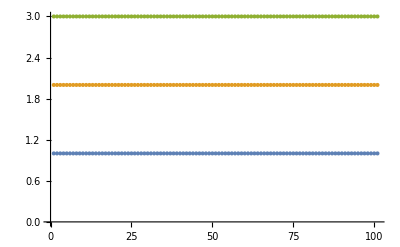

```mathematica
NumDerCentral=Table[dt2BCentral[x]/.δt->0.01/.dtB->Function[r,BesselY[0,r]],{x,2,12,0.1}];
NumDerForward=Table[2dt2BForward[x]/.δt->0.01/.dtB->Function[r,BesselY[0,r]],{x,2,12,0.1}];
NumDerBackward=Table[3dt2BBackward[x]/.δt->0.01/.dtB->Function[r,BesselY[0,r]],{x,2,12,0.1}];
ExactDerCentral=Table[Evaluate[D[BesselY[0,r],r]]/.r->x,{x,2,12,0.1}];
ListPlot[{NumDerCentral/ExactDerCentral,NumDerForward/ExactDerCentral,NumDerBackward/ExactDerCentral}]
```

### Field redefinitions and change of coordinates

#### Invert the radial coordinate r→ 1/u

```mathematica
InvRadRules={
Σ0->Function[{t,u},Σ0[t,1/u]],dpΣ0->Function[{t,u},dpΣ0[t,1/u]],
B0->Function[{t,u},B0[t,1/u]],dpB0->Function[{t,u},dpB0[t,1/u]],
A0->Function[{t,u},A0[t,1/u]],
δΣ->Function[{t,u},δΣ[t,1/u]],dpδΣ->Function[{t,u},dpδΣ[t,1/u]],
δB->Function[{t,u},δB[t,1/u]],dpδB->Function[{t,u},dpδB[t,1/u]],
δA->Function[{t,u},δA[t,1/u]]
};
```

```mathematica
EoMInverted=EEPertFuller/.r->1/u/.InvRadRules//Simplify;
```

#### Field redefinitions

```mathematica
Redefinitions={
Σ0->Function[{t,u},1/u+λ[t]+u^4*σ0[t,u]],
dpΣ0->Function[{t,u},1/2(1/u+λ[t])^2+u^2*σDot0[t,u]],
A0->Function[{t,u},1/2*(1/u+λ[t])^2+a0[t,u]],
B0->Function[{t,u},b0[t,u]*u^3],
dpB0->Function[{t,u},bDot0[t,u]*u^3],

δΣ->Function[{t,u},1/2(1/u+λ[t])+u^4*δσ[t,u]],
dpδΣ->Function[{t,u},3/4(1/u+λ[t])^2+u^2*δσDot[t,u]],
δA->Function[{t,u},1/2*(1/u+λ[t])^2+δa[t,u]],
δB->Function[{t,u},δb[t,u]*u^3],
dpδB->Function[{t,u},δbDot[t,u]*u^3]
};
```

#### We now plug in those redefinitions in the equations of motion and multiply by various powers of u, so that there are no 1 / u terms

```mathematica
EoMFacs={2*u^-4,2*u^-2,1,1};
```

```mathematica
EoMFinal=Expand[EoMFacs*EoMInverted/.Redefinitions];
```

#### Check that equations look regular at the boundary (that’s not going to be important as we will replace the equations at the boundary with the explicit boundary conditions, but it is important as we approach the boundary, so numerical values don’t go crazy)

```mathematica
EoMFinal/.u->0
```

{80 δσ[t,0]-160 σ0[t,0],-28 δσ[t,0]-8 δσDot[t,0] λ[t]+28 σ0[t,0]+16 λ[t] σDot0[t,0]-4 δσDot^(0,1)[t,0]+8 σDot0^(0,1)[t,0],9/2 b0[t,0]-9 δb[t,0],-8 a0^(0,1)[t,0]+4 δa^(0,1)[t,0]}

### Pseudospectral discretization

#### Number of collocation points and the range of u

```mathematica
NumPoints=25;
uMin=0;
uMax=1;
```

#### Set up the grid points and scale to have u_min <= u <= u_max

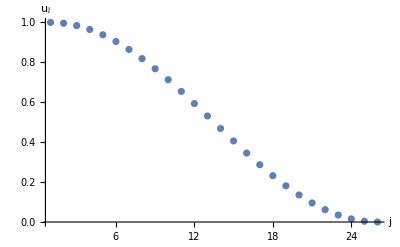

```mathematica
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
uj=uMin+(uMax-uMin)/2(1+xj);
ListPlot[uj,AxesLabel->{"j","u_j"},PlotRange->All]
```

#### Create the auxiliary array we’ll need later

```mathematica
pj=Table[If[(j==1)||(j==NumPoints+1),2,1],{j,1,NumPoints+1}];
```

#### First derivative is given by the following matrix

```mathematica
δij=IdentityMatrix[NumPoints+1];
δij[[1,1]]=(1+2 NumPoints^2)/6;
δij[[NumPoints+1,NumPoints+1]]=-(1+2 NumPoints^2)/6;
Do[δij[[j,j]]=(-xj[[j]])/(2(1-xj[[j]]^2)),{j,2,NumPoints}];Do[If[i≠j,δij[[i,j]]=(-1)^(i+j)*pj[[i]]/(pj[[j]]*(xj[[i]]-xj[[j]]))],{i,1,NumPoints+1},{j,1,NumPoints+1}];
```

#### Taking into account the Jacobian, the derivative matrix is given by:

```mathematica
DMat=2/(uMax-uMin)*δij;
```

#### Write all the elementary fields as vectors:

```mathematica
{δbVec,δbDotVec,δσVec,δσDotVec,δaVec}=
Transpose[Table[{δbj[j][t],δbDotj[j][t],δσj[j][t],δσDotj[j][t],δaj[j][t]},{j,1,NumPoints+1}]];
```

#### Derivatives of the fields are then given by:

```mathematica
dδbVec=DMat.δbVec;
dδbDotVec=DMat.δbDotVec;
dδσVec=DMat.δσVec;
ddδσVec=DMat.DMat.δσVec;
dδσDotVec=DMat.δσDotVec;
dδaVec=DMat.δaVec;
ddδaVec=DMat.DMat.δaVec;
```

#### Discretization rules (only for perturbations)

```mathematica
DiscreteRules[i_]:={
δb[t,u]->δbj[i][t],δbDot[t,u]->δbDotj[i][t],
δσ[t,u]->δσj[i][t],δσDot[t,u]->δσDotj[i][t],
δa[t,u]->δaj[i][t],
Derivative[0,1][δb][t,u]->dδbVec[[i]],Derivative[0,1][δbDot][t,u]->dδbDotVec[[i]],
Derivative[0,1][δσ][t,u]->dδσVec[[i]],Derivative[0,2][δσ][t,u]->ddδσVec[[i]],Derivative[0,1][δσDot][t,u]->dδσDotVec[[i]],
Derivative[0,1][δa][t,u]->dδaVec[[i]],Derivative[0,2][δa][t,u]->ddδaVec[[i]]
};
```

#### Prepare the background fields for later

```mathematica
BkgSaveArguments[i_]:={
b0[t,u]->b0[t,i], 
bDot0[t,u]->bDot0[t,i],
σ0[t,u]->σ0[t,i],
σDot0[t,u]->σDot0[t,i],
a0[t,u]->a0[t,i],

Derivative[0,1][b0][t,u]->db0[t,i],
Derivative[0,2][b0][t,u]->ddb0[t,i],
Derivative[0,1][bDot0][t,u]->dbDot0[t,i],
Derivative[0,1][σ0][t,u]->dσ0[t,i],
Derivative[0,2][σ0][t,u]->ddσ0[t,i],
Derivative[0,1][σDot0][t,u]->dσDot0[t,i],
Derivative[0,1][a0][t,u]->da0[t,i],
Derivative[0,2][a0][t,u]->dda0[t,i],

Derivative[2,0][b0][t,u]->dtdtb0[t,i],
Derivative[1,0][a0][t,u]->dta0[t,i]
};
```

#### Discretized equations of motion (excluding the equation at the boundary, since we’re imposing the boundary conditions there explicitly)

```mathematica
Do[EoMDiscrete[j]=Table[EoMFinal[[j]]/.DiscreteRules[i]/.BkgSaveArguments[i]/.u->uj[[i]],{i,1,NumPoints}],{j,1,4}]
```

## Module definitions

### Load & manipulate background solution

```mathematica
LoadBkgSolution:=Module[{},

(* Load the background from external files *)
FullBkgData=Get["BkgData/Bkg-"<>ToString[BkgRelevantIds[[BkgNo]]]<>".dat"];
Bkgλ=FullBkgData[[5]]//Flatten;
Bkgb=FullBkgData[[6]];
Bkgσ=FullBkgData[[7]];
BkgσDot=FullBkgData[[8]];
BkgbDot=FullBkgData[[9]];
Bkga=FullBkgData[[10]];
Bkgdtλ=FullBkgData[[11]]//Flatten;
Bkgdtb=FullBkgData[[12]];

(* Compute the radial derivatives *)
Bkgdb=Table[DMat.Bkgb[[i]],{i,1,Length[Bkgb]}];
Bkgddb=Table[DMat.DMat.Bkgb[[i]],{i,1,Length[Bkgb]}];
BkgdbDot=Table[DMat.BkgbDot[[i]],{i,1,Length[BkgbDot]}];
Bkgdσ=Table[DMat.Bkgσ[[i]],{i,1,Length[Bkgσ]}];
Bkgddσ=Table[DMat.DMat.Bkgσ[[i]],{i,1,Length[Bkgσ]}];
BkgdσDot=Table[DMat.BkgσDot[[i]],{i,1,Length[BkgσDot]}];
Bkgda=Table[DMat.Bkga[[i]],{i,1,Length[Bkga]}];
Bkgdda=Table[DMat.DMat.Bkga[[i]],{i,1,Length[Bkga]}];

(* Calculate the time derivatives we don't already have *)
Δt=0.01;
Bkgdtdtb=ConstantArray[0,{Length[Bkgdtb],NumPoints+1}];
Bkgdta=ConstantArray[0,{Length[Bkga],NumPoints+1}];
Do[
Do[
If[tn≤4,{
Bkgdtdtb[[tn,un]]=1/Δt*Sum[ForwardCoeffs[[i]]*Bkgdtb[[tn+(i-1),un]],{i,1,Length[ForwardCoeffs]}];
Bkgdta[[tn,un]]=1/Δt*Sum[ForwardCoeffs[[i]]*Bkga[[tn+(i-1),un]],{i,1,Length[ForwardCoeffs]}];}];
If[tn≥5&&tn≤Length[Bkgdtb]-4,{
Bkgdtdtb[[tn,un]]=1/Δt*Sum[CentralCoeffs[[i]]*Bkgdtb[[tn-(5-i),un]],{i,1,Length[CentralCoeffs]}];
Bkgdta[[tn,un]]=1/Δt*Sum[CentralCoeffs[[i]]*Bkga[[tn-(5-i),un]],{i,1,Length[CentralCoeffs]}];}];
If[tn≥Length[Bkgdtb]-3,{
Bkgdtdtb[[tn,un]]=1/Δt*Sum[BackwardCoeffs[[i]]*Bkgdtb[[tn-(7-i),un]],{i,1,Length[BackwardCoeffs]}];
Bkgdta[[tn,un]]=1/Δt*Sum[BackwardCoeffs[[i]]*Bkga[[tn-(7-i),un]],{i,1,Length[BackwardCoeffs]}];}];
,{tn,1,Length[Bkgdtb]}];
,{un,1,NumPoints+1}];

(* Rules for including the explicit background values *)
BkgRules[tn_,un_]:={
λ[t]->Bkgλ[[tn]],
λ'[t]->Bkgdtλ[[tn]],
b0[t,un]->Bkgb[[tn,un]],
σ0[t,un]->Bkgσ[[tn,un]],
σDot0[t,un]->BkgσDot[[tn,un]],
bDot0[t,un]->BkgbDot[[tn,un]],
a0[t,un]->Bkga[[tn,un]],
db0[t,un]->Bkgdb[[tn,un]],
ddb0[t,un]->Bkgddb[[tn,un]],
dbDot0[t,un]->BkgdbDot[[tn,un]],
dσ0[t,un]->Bkgdσ[[tn,un]],
ddσ0[t,un]->Bkgddσ[[tn,un]],
dσDot0[t,un]->BkgdσDot[[tn,un]],
da0[t,un]->Bkgda[[tn,un]],
dda0[t,un]->Bkgdda[[tn,un]],
dtdtb0[t,un]->Bkgdtdtb[[tn,un]],
dta0[t,un]->Bkgdta[[tn,un]]
};
];
```

### Solve EoMs at initial time

```mathematica
SolveAtInitialTime:=Module[{},
(* Initial conditions *)
MyBInit=FullBkgData[[2]];
δbInitRules=Table[δbj[j][t0]->-1/2*MyBInit[[j]],{j,1,NumPoints+1}]; (* SIMPLEST IC FOR VANISHING INITIAL δ(Δp) *)

(* First nested equation *)
δσBCInitRule={δσj[NumPoints+1][t0]->0};
EoMD1Init=Table[EoMDiscrete[1][[i]]/.BkgRules[1,i]/.t->t0/.δbInitRules/.δσBCInitRule,{i,1,NumPoints}];
δσSolInitRules=NSolve[Table[EoMD1Init[[j]]==0,{j,1,NumPoints}],δσVec[[1;;NumPoints]]/.t->t0];
δσSolInitRules=Join[δσSolInitRules[[1]],δσBCInitRule];
BkgσList=Table[{uj[[j]],Bkgσ[[1,j]]},{j,1,NumPoints+1}];
δσList=Table[{uj[[j]],δσj[j][t0]},{j,1,NumPoints+1}]/.δσSolInitRules;

(* Choose Subscript[λ, GB] *)
λGBChoiceRule={λGB->-0.1};

(* Second nested equation *)
a40Rule={a40->-1/2};
EnDensBkg=1/2 τabValues[[1,1]]/.τSol/.lcSym->1/.a[2][t]->a40/.a40Rule//Simplify;
EnDensPert=1/2 τabValues[[1,1]]/.τSol/.lcSym->lc/.a[2][t]->a40+λGB*δa4/.a40Rule//Simplify;
δa4Sol=Solve[EnDensBkg==EnDensPert,δa4][[1]]//Simplify;
δa4Sol={δa4->-1/4}; (* EQUAL ENERGY DENSITIES *)
δσDotBCInitRule ={δσDotj[NumPoints+1][t0]->1/2*a40+δa4};
EoMD2Init=Table[EoMDiscrete[2][[i]]/.BkgRules[1,i]/.t->t0/.δσSolInitRules/.δσDotBCInitRule/.a40Rule/.δa4Sol/.λGBChoiceRule,{i,1,NumPoints}];
δσDotSolInitRules=NSolve[Table[EoMD2Init[[j]]==0,{j,1,NumPoints}],δσDotVec[[1;;NumPoints]]/.t->t0];
δσDotSolInitRules=Join[δσDotSolInitRules[[1]],δσDotBCInitRule/.a40Rule/.δa4Sol/.λGBChoiceRule];
BkgσDotList=Table[{uj[[j]],BkgσDot[[1,j]]},{j,1,NumPoints+1}];
δσDotList=Table[{uj[[j]],δσDotj[j][t0]},{j,1,NumPoints+1}]/.δσDotSolInitRules;

(* Third nested equation *)
g1140=Bkgdb[[1,NumPoints+1]];
δg114=dδbVec[[NumPoints+1]]/.t->t0/.δbInitRules;
δbDotBCInitRule={δbDotj[NumPoints+1][t0]->-2*(g1140+δg114)};
EoMD3Init=Table[EoMDiscrete[3][[i]]/.BkgRules[1,i]/.t->t0/.δbInitRules/.δσSolInitRules/.δσDotSolInitRules/.δbDotBCInitRule,{i,1,NumPoints}];
δbDotInitRules=NSolve[Table[EoMD3Init[[j]]==0,{j,1,NumPoints}],δbDotVec[[1;;NumPoints]]/.t->t0];
δbDotInitRules=Join[δbDotInitRules[[1]],δbDotBCInitRule];
BkgbDotList=Table[{uj[[j]],BkgbDot[[1,j]]},{j,1,NumPoints+1}];
δbDotList=Table[{uj[[j]],δbDotj[j][t0]},{j,1,NumPoints+1}]/.δbDotInitRules;

(* Fourth nested equation *)
δaBCInitRule={δaj[NumPoints+1][t0]->0};
EoMD4Init=Table[EoMDiscrete[4][[i]]/.BkgRules[1,i]/.t->t0/.δσSolInitRules/.δbInitRules/.δσDotSolInitRules/.δbDotInitRules/.δaBCInitRule,{i,1,NumPoints}];
δaInitRules=NSolve[Table[EoMD4Init[[j]]==0,{j,1,NumPoints}],δaVec[[1;;NumPoints]]/.t->t0];
δaInitRules=Join[δaInitRules[[1]],δaBCInitRule];
BkgaList=Table[{uj[[j]],Bkga[[1,j]]},{j,1,NumPoints+1}];
δaList=Table[{uj[[j]],δaj[j][t0]},{j,1,NumPoints+1}]/.δaInitRules;

(* Extract time derivative of δb *)
dtδb=r^3*Derivative[1,0][δB][t,r]/.dpδRules/.r->1/u/.InvRadRules/.Redefinitions//Expand//Simplify;
dtδbValuesInit=Join[Table[dtδb/.DiscreteRules[i]/.BkgSaveArguments[i]/.u->uj[[i]]/.BkgRules[1,i]/.t->t0/.δbInitRules/.δaInitRules/.δbDotInitRules,{i,1,NumPoints}],{0}];
dtδbInitRules=Table[dtδb[i][t0]->dtδbValuesInit[[i]],{i,1,NumPoints+1}];
];
```

### Solve EoMs at any time

```mathematica
SolveEoM1[tnLocal_]:=Module[{tn=tnLocal},
δσBCRule={δσj[NumPoints+1][tn]->0};
EoMD1=Table[EoMDiscrete[1][[i]]/.BkgRules[tn,i]/.t->tn/.δbRules/.δσBCRule,{i,1,NumPoints}];
δσSolRules=NSolve[Table[EoMD1[[j]]==0,{j,1,NumPoints}],δσVec[[1;;NumPoints]]/.t->tn];
δσSolRules=Join[δσSolRules[[1]],δσBCRule];
];
```

```mathematica
SolveEoM2[tnLocal_]:=Module[{tn=tnLocal},
δσDotBCRule ={δσDotj[NumPoints+1][tn]->1/2*a40+δa4};
EoMD2=Table[EoMDiscrete[2][[i]]/.BkgRules[tn,i]/.t->tn/.δσSolRules/.δσDotBCRule/.a40Rule/.δa4Sol/.λGBChoiceRule,{i,1,NumPoints}];
δσDotSolRules=NSolve[Table[EoMD2[[j]]==0,{j,1,NumPoints}],δσDotVec[[1;;NumPoints]]/.t->tn];
δσDotSolRules=Join[δσDotSolRules[[1]],δσDotBCRule/.a40Rule/.δa4Sol/.λGBChoiceRule];
];
```

```mathematica
SolveEoM3[tnLocal_]:=Module[{tn=tnLocal},
g1140=Bkgdb[[tn,NumPoints+1]];
δg114=dδbVec[[NumPoints+1]]/.t->tn/.δbRules;
δbDotBCRule={δbDotj[NumPoints+1][tn]->-2*(g1140+δg114)};
EoMD3=Table[EoMDiscrete[3][[i]]/.BkgRules[tn,i]/.t->tn/.δbRules/.δσSolRules/.δσDotSolRules/.δbDotBCRule,{i,1,NumPoints}];
δbDotRules=NSolve[Table[EoMD3[[j]]==0,{j,1,NumPoints}],δbDotVec[[1;;NumPoints]]/.t->tn];
δbDotRules=Join[δbDotRules[[1]],δbDotBCRule];
];
```

```mathematica
SolveEoM4[tnLocal_]:=Module[{tn=tnLocal},
δaBCRule={δaj[NumPoints+1][tn]->0};
EoMD4=Table[EoMDiscrete[4][[i]]/.BkgRules[tn,i]/.t->tn/.δσSolRules/.δbRules/.δσDotSolRules/.δbDotRules/.δaBCRule,{i,1,NumPoints}];
δaRules=NSolve[Table[EoMD4[[j]]==0,{j,1,NumPoints}],δaVec[[1;;NumPoints]]/.t->tn];
δaRules=Join[δaRules[[1]],δaBCRule];
];
```

```mathematica
FindTimeDerivatives[tnLocal_]:=Module[{tn=tnLocal},
dtδbValues=Join[Table[dtδb/.DiscreteRules[i]/.BkgSaveArguments[i]/.u->uj[[i]]/.BkgRules[tn,i]/.t->tn/.δbRules/.δaRules/.δbDotRules,{i,1,NumPoints}],{0}];
dtδbRules=Table[dtδb[i][tn]->dtδbValues[[i]],{i,1,NumPoints+1}];
];
```

### Runge-Kutta and Adams-Bashworth setup

```mathematica
αRK4=ConstantArray[0,{4,4}];
αRK4[[2,1]]=1/2;
αRK4[[3,2]]=1/2;
αRK4[[4,3]]=1;
```

```mathematica
kδbVec=ConstantArray[0,{NumPoints+1,4}];
```

```mathematica
bRK4={1/6,1/3,1/3,1/6};
```

```mathematica
Δt=0.01;
```

```mathematica
AB4Coeffs={55/24,-59/24,37/24,-3/8};
```

### Runge-Kutta evolution

```mathematica
RungeKuttaEvolution:=Module[{},
Clear[tnLocal];
RKSteps=TotalTimeSteps;
StartTime=SessionTime[];
Do[
Do[
δbLocalValues=Table[(δbj[ib][tnLocal]/.δbRulesThisTimestep)+(αRK4.kδbVec[[ib]])[[iRK]]*Δt,{ib,1,NumPoints+1}];
δbRules=Table[δbj[ib][tnLocal]->δbLocalValues[[ib]],{ib,1,NumPoints+1}];
SolveEoM1[tnLocal];
SolveEoM2[tnLocal];
SolveEoM3[tnLocal];
SolveEoM4[tnLocal];
FindTimeDerivatives[tnLocal];
If[iRK==1,dtδbSave=Append[dtδbSave,Table[dtδb[ii][tnLocal]/.dtδbRules,{ii,1,NumPoints+1}]];];
Do[kδbVec[[ib]][[iRK]]=dtδb[ib][tnLocal]/.dtδbRules,{ib,1,NumPoints+1}];
,{iRK,1,4}];
δbNewValues=Table[δbj[i][tnLocal]+(kδbVec[[i]].bRK4)*Δt,{i,1,NumPoints+1}]/.δbRulesThisTimestep;
δbEvolvedValues=Append[δbEvolvedValues,δbNewValues];
δbRulesThisTimestep=Table[δbj[i][tnLocal+1]->δbNewValues[[i]],{i,1,NumPoints+1}];
NowTime=SessionTime[];
AvTimePerStep=(NowTime-StartTime)/tnLocal;
RemainingTime=AvTimePerStep*(TotalTimeSteps-tnLocal);
TotalRemainingTime=AvTimePerStep*(TotalNumberOfIterations-tnLocal);
NumMin=Quotient[Round[RemainingTime],60];
If[NumMin<10,NumMinText="0"<>ToString[NumMin],NumMinText=ToString[NumMin]];
NumSec=Mod[Round[RemainingTime],60];
If[NumSec<10,NumSecText="0"<>ToString[NumSec],NumSecText=ToString[NumSec]];
NumMinTotal=Quotient[Round[TotalRemainingTime],60];
If[NumMinTotal<10,NumMinTextTotal="0"<>ToString[NumMinTotal],NumMinTextTotal=ToString[NumMinTotal]];
NumSecTotal=Mod[Round[TotalRemainingTime],60];
If[NumSecTotal<10,NumSecTextTotal="0"<>ToString[NumSecTotal],NumSecTextTotal=ToString[NumSecTotal]];
,{tnLocal,1,RKSteps}];
];
```

## EXEC {Automatization}

### Choose the backgrounds

#### See all the available backgrounds that don’t have perturbative results

```mathematica
BkgIdFiles=FileNames["Bkg-*",{"BkgData"}];
PertIdFiles=FileNames["Pert-*",{"PertData"}];
BkgIds=Table[StringTake[BkgIdFiles[[i]],{13,15}],{i,1,Length[BkgIdFiles]}];
PertIds=Table[StringTake[PertIdFiles[[i]],{15,17}],{i,1,Length[PertIdFiles]}];
BkgRelevantIds=Complement[BkgIds,PertIds]
```

{001,002,003,004,005,006,007,008,009,010,011,012,013,014,015,016,017,018,019,020,021,022,023,024,025}

#### Choose which one of these you want -- NOTE: errors are okay if all the backgrounds already have the perturbations

```mathematica
BkgChoice=Table[i,{i,1,25}];
BkgRelevantIds[[BkgChoice]]
```

{001,002,003,004,005,006,007,008,009,010,011,012,013,014,015,016,017,018,019,020,021,022,023,024,025}

#### Total number of steps

```mathematica
TotalNumberOfIterations=0;
Do[
BkgNo=BkgNoLocal;
FullBkgData=Get["BkgData/Bkg-"<>ToString[BkgRelevantIds[[BkgNo]]]<>".dat"];
TotalNumberOfIterations=TotalNumberOfIterations+Length[FullBkgData[[5]]];
,{BkgNoLocal,BkgChoice}]
TotalNumberOfIterations
```

7205

### Main loop

```mathematica
BkgCnt=1;
Do[

(* Load background and solve at initial time *)
BkgNo=BkgNoLocal;
LoadBkgSolution;
SolveAtInitialTime;
δbRules=δbInitRules/.t0->tn;

(* Initialize time evolution loop *)
TotalTimeSteps=Length[Bkgλ];
kδbVec=ConstantArray[0,{NumPoints+1,4}];
δbRulesThisTimestep=δbInitRules/.t0->1;
δbEvolvedValues={Table[δbj[i][1],{i,1,NumPoints+1}]/.δbRulesThisTimestep};
dtδbSave={};

(* Time evolution *)
RungeKuttaEvolution;
AdamsBashworthEvolution;

(* Export results *)
ExportFileName="PertData/Pert-"<>BkgRelevantIds[[BkgNo]]<>".dat";
Export[ExportFileName,δbEvolvedValues];

(* Iterators *)
TotalNumberOfIterations=TotalNumberOfIterations-TotalTimeSteps;
BkgCnt=BkgCnt+1;

,{BkgNoLocal,BkgChoice}]
```

$Aborted

### Monitor progress

```mathematica
Dynamic["Background "<>ToString[BkgCnt]<>" / "<>ToString[Length[BkgChoice]]<>"\n---------------------\n"<>"Step: "<>ToString[tnLocal]<>" / "<>ToString[TotalTimeSteps]<>"\n"<>"Remaining time: "<>ToString[NumMinText]<>":"<>ToString[NumSecText]<>"\n---------------------\nTotal time left: "<>ToString[NumMinTextTotal]<>":"<>ToString[NumSecTextTotal]]
```

## Analyze results

### Load all the backgrounds and perturbed results

```mathematica
BkgIdFilesPert=FileNames["Pert-*",{"PertData"}];
BkgIdsPert=Table[StringTake[BkgIdFilesPert[[i]],{15,17}],{i,1,Length[BkgIdFilesPert]}]
NBkgsPert=Length[BkgIdsPert];
```

{001,002,003,004,005,006,007,008,009,010,011,012,013,014,015,016,017,018,019,020,021,022,023,024,025}

```mathematica
Do[
FullBkgDataMultiple=Get["BkgData/Bkg-"<>BkgIdsPert[[bi]]<>".dat"];
BkgbMultiple[bi]=FullBkgDataMultiple[[6]];
BkgdbMultiple[bi]=Table[DMat.BkgbMultiple[bi][[i]],{i,1,Length[BkgbMultiple[bi]]}];
δbImport[bi]=Import["PertData/Pert-"<>BkgIdsPert[[bi]]<>".dat"];
,{bi,1,NBkgsPert}]
```

```mathematica
bForms=Table[Get["BkgData/Bkg-"<>BkgIdsPert[[bi]]<>".dat"][[2]],{bi,1,NBkgsPert}];
```

### Get expressions for pressure and temperature

#### We know the static black hole solution

```mathematica
fGB[u_]:=1/(2λGB)*(1-√(1-4*λGB*(1-u^4*((π*T)/aGB)^4)));
aGBRule={aGB->√(1/2(1+√(1-4*λGB)))};
```

#### The tt component of the metric of the static solution is

```mathematica
TTStatic=-1/u^2*fGB[u];
```

#### The first coefficient in the expansion must match the first coefficient of -2A:

```mathematica
FirstCoeff=SeriesCoefficient[TTStatic,{u,0,-2}]/.aGB->1;
ShouldBeZero=FirstCoeff+1/lc^2//Simplify
```

0

#### From the second coefficient, we can extract a4 in equilibrium

```mathematica
SecondCoeff=SeriesCoefficient[TTStatic,{u,0,2}]/.aGB->1;
a4EqRule=Solve[-2a4Eq==SecondCoeff,a4Eq][[1]]
```

{a4Eq→-(π^4 T^4)/(2 √(1-4 λGB))}

#### Hence, hatted pressure in equilibrium is then

```mathematica
pEqHatted=1/2 τabValues[[2,2]]/.τSol/. b[4][t]->0/.a[2][t]->a4Eq/.a4EqRule/.lcSym->lc//Simplify
```

(π^4 T^4)/(√2 (1+√(1-4 λGB))^(3/2))

#### Similarly, hatted energy density it then given by

```mathematica
ϵEqHatted=1/2 τabValues[[1,1]]/.τSol/. b[4][t]->0/.a[2][t]->a4Eq/.a4EqRule/.lcSym->lc//Simplify
```

(3 π^4 T^4)/(√2 (1+√(1-4 λGB))^(3/2))

#### Hatted energy density

```mathematica
EnDensBkg=1/2 τabValues[[1,1]]/.τSol/.lcSym->1/.a[2][t]->-1/2
```

3/4

#### The hatted equilibrium pressure is, of course, a third of that

```mathematica
TSol=Solve[EnDensBkg==ϵEqHatted,T][[4]]
```

{T→(1+√(1-4 λGB))^(3/8)/(2^(3/8) π)}

```mathematica
T/.TSol/.λGB->0
```

1/π

#### The hatted equilibrium pressure is however the same as in the zero-λGB case, since the theory is conformal

```mathematica
pEqHatted/.TSol
```

1/4

#### In general, the expression for the pressure is given by

```mathematica
δpHatted=(1/2 τabValues[[4,4]]-1/2(1/2 τabValues[[2,2]]+1/2 τabValues[[3,3]]))/.τSol//Simplify
```

(3 (1-2 lcSym^2) b[4][t])/lcSym^5

### Pressure anisotropy

#### Generate relative pressure anisotropies for both the background and perturbed solutions as functions of t*T, noting that some solutions have different final T

```mathematica
Do[
δpRelBkg[bi]={};
δpRelFull[bi]={};
Do[
dbAtBoundaryLocal=BkgdbMultiple[bi][[i]][[NumPoints+1]];
δpHattedBkgLocal=δpHatted/.lcSym->1/.b[4][t]->dbAtBoundaryLocal;
δpRelBkg[bi]=Append[δpRelBkg[bi],{Δt*(i-1)*(T/.TSol/.λGB->0),δpHattedBkgLocal/(pEqHatted/.TSol)}];
δbValLoc=δbImport[bi][[i]];
δbLocRules=Table[δbj[j][t]->δbValLoc[[j]],{j,1,NumPoints+1}];
dδbAtBoundaryLocal=dδbVec[[NumPoints+1]]/.δbLocRules;
δpHattedFullLocal=δpHatted/.lcSym->lc/.b[4][t]->(dbAtBoundaryLocal+λGB*dδbAtBoundaryLocal)/.λGB->-0.1;
δpRelFull[bi]=Append[δpRelFull[bi],{Δt*(i-1)*(T/.TSol/.λGB->0),δpHattedFullLocal/(pEqHatted/.TSol)}];
,{i,1,Length[BkgdbMultiple[bi]]}]
,{bi,1,NBkgsPert}]
```

#### Select a few backgrounds and show their pressure anisotropies

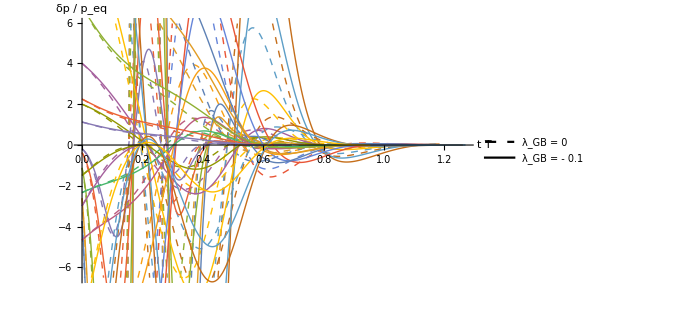

```mathematica
BkgToShow=Table[i,{i,1,NBkgsPert}];
PressureBkgPlot=ListPlot[Table[δpRelBkg[bi],{bi,BkgToShow}],Joined->True,AxesLabel->{Style["t T",FontSize->18,Bold,Italic],Style["δp / p_eq",FontSize->18,Bold,Italic]}(*,PlotRange->All*),ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->{{Dashed,Thick}}];
PressureFullPlot=ListPlot[Table[δpRelFull[bi],{bi,BkgToShow}],Joined->True,AxesLabel->{Style["t T",FontSize->18,Bold,Italic],Style["δp / p_eq",FontSize->18,Bold,Italic]},PlotRange->All,ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->Thick,PlotLegends->Placed[LineLegend[{{Black,Dashed},Black},{Style["λ_GB = 0",FontSize->16,Italic],Style["λ_GB = - 0.1",FontSize->16,Italic]}],{Scaled[{0.6,0.9}], {0, 0.5}}]];
ICPlots=Plot[Evaluate[Table[bForms[[bi]],{bi,BkgToShow}]],{u,0,1},AxesLabel->{Style["u",FontSize->18,Bold,Italic],Style["b_(0, init)(u)",FontSize->18,Bold,Italic]},PlotRange->All,ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->Thick];
Show[PressureBkgPlot,PressureFullPlot]
```

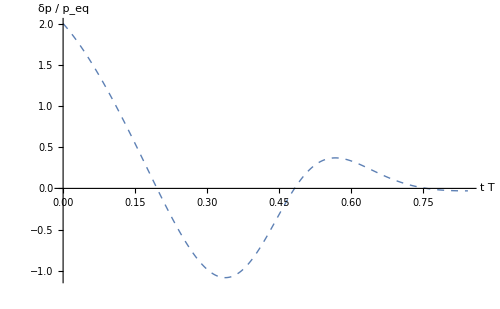

```mathematica
ListPlot[Table[δpRelBkg[bi],{bi,10,10}],Joined->True,AxesLabel->{Style["t T",FontSize->18,Bold,Italic],Style["δp / p_eq",FontSize->18,Bold,Italic]}(*,PlotRange->All*),ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->{{Dashed,Thick}}]
```

```mathematica
(*Export["PressurePlotVariousIC.pdf",Show[PressureBkgPlot,PressureFullPlot]];
Export["ICPlotVariousIC.pdf",ICPlots];*)
```

## Fit to QNM evolution

### Load the QNM data

#### Load the data, the format is {λGB, { {ωQNM , Re ϕ , Im ϕ }_i }}

```mathematica
SetDirectory[NotebookDirectory[]];
DataQNM=Import["QNM_GB_v1.m"]; (* just change this file *)
```

#### How many modes

```mathematica
NoQNM=Length[DataQNM[[1,2]]]
```

10

```mathematica
(*NoQNM=5;*)
```

### Manipulate the zero λ_GB data

#### Use the same grid as in the data

```mathematica
uMin=0;
uMax=1;
NumPoints=Length[DataQNM[[1,2,1,2]]]-1
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
uj=(uMin+(uMax-uMin)/2(1+xj));
xRule=Solve[uSym==uMin+(uMax-uMin)/2(1+xSym),xSym][[1]];
```

50

#### Check that the λGB = 0 is in the middle of the data

```mathematica
λGBZeroIndex=Quotient[Length[DataQNM],2]+1;
ShouldBeZero=DataQNM[[λGBZeroIndex,1]]
```

0.

#### Interpolate all QNM wave functions with Chebyshev polynomials

```mathematica
fTemp[u_]=Sum[α[n]*ChebyshevT[n-1,xSym/.xRule],{n,1,NumPoints+1}]/.uSym->u;
Do[
Reb0Data[iQNM]=DataQNM[[λGBZeroIndex,2,iQNM,2]];
CoeffRules=Solve[Table[fTemp[uj[[j]]]==Reverse[Reb0Data[iQNM][[;;,2]]][[j]],{j,1,NumPoints+1}],Table[α[n],{n,1,NumPoints+1}]][[1]];
Reb0[iQNM][u_]=fTemp[u]/.CoeffRules;
Imb0Data[iQNM]=DataQNM[[λGBZeroIndex,2,iQNM,3]];
CoeffRules=Solve[Table[fTemp[uj[[j]]]==Reverse[Imb0Data[iQNM][[;;,2]]][[j]],{j,1,NumPoints+1}],Table[α[n],{n,1,NumPoints+1}]][[1]];
Imb0[iQNM][u_]=fTemp[u]/.CoeffRules;
,{iQNM,1,NoQNM}]
```

#### Plot them

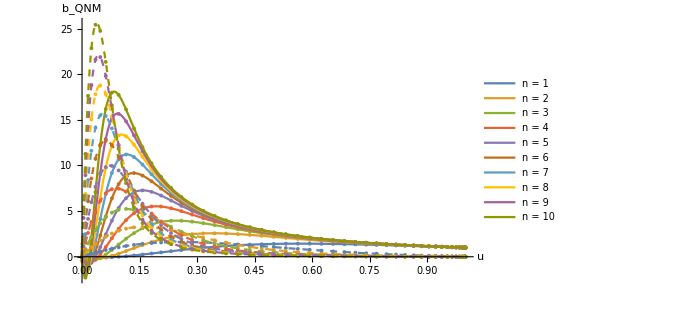

```mathematica
QNMRePlot=Show[ListPlot[Table[Reb0Data[iQNM],{iQNM,1,NoQNM}],PlotRange->All],Plot[Evaluate[Table[Reb0[iQNM][u],{iQNM,1,NoQNM}]],{u,0,1},PlotStyle->{{Thick}},PlotLegends->Table["n = "<>ToString[i],{i,1,NoQNM}],PlotRange->All],PlotRange->All,AxesLabel->{"u","b_QNM"},ImageSize->500];
QNMImPlot=Show[ListPlot[Table[Imb0Data[iQNM],{iQNM,1,NoQNM}],PlotRange->All],Plot[Evaluate[Table[Imb0[iQNM][u],{iQNM,1,NoQNM}]],{u,0,1},PlotStyle->{{Thick,Dashed}},PlotRange->All],PlotRange->All,AxesLabel->{"u","b_QNM"},ImageSize->500];
Show[QNMRePlot,QNMImPlot]
```

#### Extract QNM frequencies

```mathematica
Do[
Reω0[iQNM]=Re[DataQNM[[λGBZeroIndex,2,iQNM,1]]];
Imω0[iQNM]=Im[DataQNM[[λGBZeroIndex,2,iQNM,1]]];
,{iQNM,1,NoQNM}]
```

#### Find the first derivatives of b at the boundary (for pressure)

```mathematica
Do[
ReDb0[iQNM]=Reb0[iQNM]'[0];
ImDb0[iQNM]=Imb0[iQNM]'[0];
,{iQNM,1,NoQNM}]
```

### Manipulate the nonzero λ_GB data

#### The format is {λGB, { {ωQNM , Re ϕ , Im ϕ }_i }}

#### How many λGB values do we have

```mathematica
λGBValues=Length[DataQNM]
```

11

#### I need real and imaginary parts of ω as a function of λGB

```mathematica
Do[
Reω[iQNM]={};
Imω[iQNM]={};
Do[
λGBLocal=DataQNM[[iλGB]][[1]];
ωLocal=DataQNM[[iλGB,2,iQNM,1]];
Reω[iQNM]=Append[Reω[iQNM],{λGBLocal,Re[ωLocal]}];
Imω[iQNM]=Append[Imω[iQNM],{λGBLocal,Im[ωLocal]}];
,{iλGB,1,λGBValues}];
,{iQNM,1,NoQNM}]
```

#### Linearize the temperature around the eq. value

```mathematica
δT=-3/(8 π);
```

#### Find the slopes at λGB = 0, i.e. δω

```mathematica
Do[
ReωLocalInt=Interpolation[Reω[iQNM]];
ImωLocalInt=Interpolation[Imω[iQNM]];
Reδω[iQNM]=ReωLocalInt'[0](*+δT*ReωLocalInt[0]*);
Imδω[iQNM]=ImωLocalInt'[0](*+δT*ImωLocalInt[0]*);
,{iQNM,1,NoQNM}]
```

#### Check it worked out

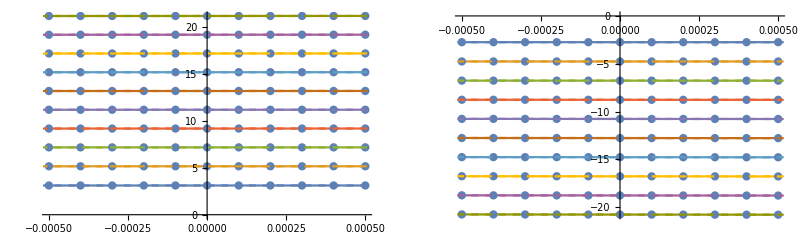

```mathematica
ReωPlot=Show[
ListPlot[Table[Reω[iQNM],{iQNM,1,NoQNM}],Joined->True,Mesh->Full,PlotRange->All],
Plot[Evaluate[Table[{Reδω[iQNM]*λGB+Reω0[iQNM]},{iQNM,1,NoQNM}]],{λGB,-0.1,0.1},PlotStyle->Dashed]];
ImωPlot=Show[
ListPlot[Table[Imω[iQNM],{iQNM,1,NoQNM}],Joined->True,Mesh->Full,PlotRange->All],
Plot[Evaluate[Table[{Imδω[iQNM]*λGB+Imω0[iQNM]},{iQNM,1,NoQNM}]],{λGB,-0.1,0.1},PlotStyle->Dashed]];
GraphicsGrid[{{ReωPlot,ImωPlot}},ImageSize->800]
```

#### Get the GB modes as a function of λGB (the format is {λGB, { {ωQNM , Re ϕ , Im ϕ }_i }})

```mathematica
fTemp[u_]=Sum[α[n]*ChebyshevT[n-1,xSym/.xRule],{n,1,NumPoints+1}]/.uSym->u;
Do[
RedbList[iQNM]={};
ImdbList[iQNM]={};
Do[
λGBLocal=DataQNM[[iλGB]][[1]];
RebDataLocal=DataQNM[[iλGB,2,iQNM,2]][[;;,2]];
ImbDataLocal=DataQNM[[iλGB,2,iQNM,3]][[;;,2]];
CoeffRules=Solve[Table[fTemp[uj[[j]]]==Reverse[RebDataLocal][[j]],{j,1,NumPoints+1}],Table[α[n],{n,1,NumPoints+1}]][[1]];
RebLocal[u_]=fTemp[u]/.CoeffRules;
CoeffRules=Solve[Table[fTemp[uj[[j]]]==Reverse[ImbDataLocal][[j]],{j,1,NumPoints+1}],Table[α[n],{n,1,NumPoints+1}]][[1]];
ImbLocal[u_]=fTemp[u]/.CoeffRules;
RedbList[iQNM]=Append[RedbList[iQNM],{λGBLocal,RebLocal'[0]}];
ImdbList[iQNM]=Append[ImdbList[iQNM],{λGBLocal,ImbLocal'[0]}];
,{iλGB,1,λGBValues}];
,{iQNM,1,NoQNM}]
```

#### Find the slopes at λGB = 0, i.e. δb’

```mathematica
Do[
RedbLocalInt=Interpolation[RedbList[iQNM]];
ImdbLocalInt=Interpolation[ImdbList[iQNM]];
Reδdb[iQNM]=RedbLocalInt'[0](*+π*δT*ReDb0[iQNM]*);
Imδdb[iQNM]=ImdbLocalInt'[0](*+π*δT*ImDb0[iQNM]*);
,{iQNM,1,NoQNM}]
```

#### Check it worked out

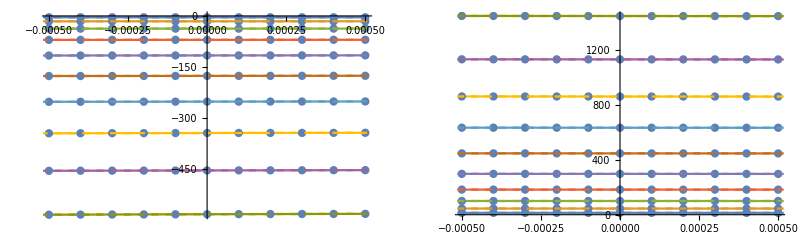

```mathematica
RedbPlot=Show[
ListPlot[Table[RedbList[iQNM],{iQNM,1,NoQNM}],Joined->True,Mesh->Full,PlotRange->All],
Plot[Evaluate[Table[{Reδdb[iQNM]*λGB+ReDb0[iQNM]},{iQNM,1,NoQNM}]],{λGB,-0.1,0.1},PlotStyle->Dashed]];
ImdbPlot=Show[
ListPlot[Table[ImdbList[iQNM],{iQNM,1,NoQNM}],Joined->True,Mesh->Full,PlotRange->All],
Plot[Evaluate[Table[{Imδdb[iQNM]*λGB+ImDb0[iQNM]},{iQNM,1,NoQNM}]],{λGB,-0.1,0.1},PlotStyle->Dashed]];
GraphicsGrid[{{RedbPlot,ImdbPlot}},ImageSize->800]
```

#### Find the δb

```mathematica
Do[
Reδb[iQNM]={};
Imδb[iQNM]={};
Do[
RebLocalList={};
ImbLocalList={};
Do[
λGBLocal=DataQNM[[iλGB]][[1]];
RebLocalData=DataQNM[[iλGB,2,iQNM,2]][[n,2]];
ImbLocalData=DataQNM[[iλGB,2,iQNM,3]][[n,2]];
RebLocalList=Append[RebLocalList,{λGBLocal,RebLocalData}];
ImbLocalList=Append[ImbLocalList,{λGBLocal,ImbLocalData}];
,{iλGB,1,λGBValues}];
uLocal=DataQNM[[1,2,iQNM,2]][[n,1]];
RebLocalInt=Interpolation[RebLocalList];
ImbLocalInt=Interpolation[ImbLocalList];
Reδb[iQNM]=Append[Reδb[iQNM],{uLocal,RebLocalInt'[0](*+π*δT*uLocal*Reb0[iQNM]'[uLocal]*)}];
Imδb[iQNM]=Append[Imδb[iQNM],{uLocal,ImbLocalInt'[0](*+π*δT*uLocal*Imb0[iQNM]'[uLocal]*)}];
,{n,1,NumPoints+1}];
Reδb[iQNM]=Reverse[Reδb[iQNM]];
Imδb[iQNM]=Reverse[Imδb[iQNM]];
,{iQNM,1,NoQNM}]
```

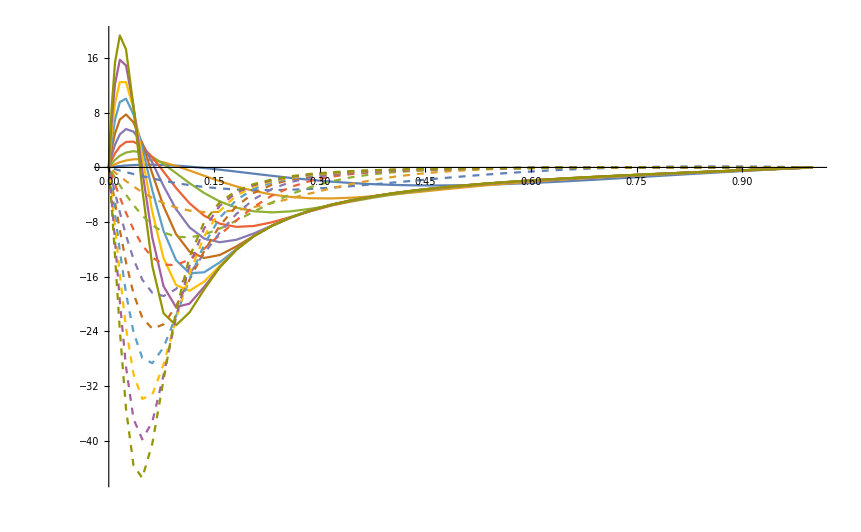

```mathematica
Show[
ListPlot[Table[Reδb[iQNM],{iQNM,1,NoQNM}],Joined->True,PlotRange->All],
ListPlot[Table[Imδb[iQNM],{iQNM,1,NoQNM}],Joined->True,PlotRange->All,PlotStyle->{{Dashed}}],PlotRange->All]
```

#### Interpolate them

```mathematica
fTemp[u_]=Sum[α[n]*ChebyshevT[n-1,xSym/.xRule],{n,1,NumPoints+1}]/.uSym->u;
Do[
CoeffRules=Solve[Table[fTemp[uj[[j]]]==Reδb[iQNM][[j,2]],{j,1,NumPoints+1}],Table[α[n],{n,1,NumPoints+1}]][[1]];
ReδbInt[iQNM][u_]=fTemp[u]/.CoeffRules;
CoeffRules=Solve[Table[fTemp[uj[[j]]]==Imδb[iQNM][[j,2]],{j,1,NumPoints+1}],Table[α[n],{n,1,NumPoints+1}]][[1]];
ImδbInt[iQNM][u_]=fTemp[u]/.CoeffRules;
,{iQNM,1,NoQNM}]
```

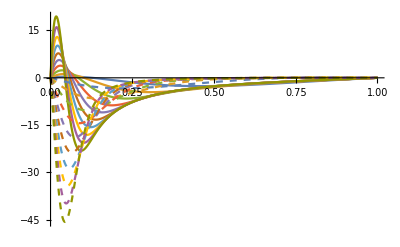

```mathematica
Show[
Plot[Evaluate[Table[ReδbInt[iQNM][u],{iQNM,1,NoQNM}]],{u,0,1},PlotRange->All],
Plot[Evaluate[Table[ImδbInt[iQNM][u],{iQNM,1,NoQNM}]],{u,0,1},PlotRange->All,PlotStyle->Dashed]]
```

```mathematica
Table[Reδdb[i],{i,1,NoQNM}]
Table[Imδdb[i],{i,1,NoQNM}]
```

{15.2446,61.6655,148.498,284.024,475.786,730.606,1054.84,1454.47,1935.17,2498.82}

{-29.2362,-84.6313,-168.12,-276.98,-407.361,-554.741,-714.048,-879.876,-1046.53,-1204.96}

```mathematica
Table[Abs[(ReδbInt[i]'[0]-Reδdb[i])/Reδdb[i]],{i,1,NoQNM}]
```

{3.44973×10^-9,2.30385×10^-9,1.07994×10^-9,4.56312×10^-10,1.59189×10^-9,1.85443×10^-9,7.99043×10^-10,1.05126×10^-9,6.30107×10^-10,6.54712×10^-10}

```mathematica
Table[Abs[(ImδbInt[i]'[0]-Imδdb[i])/Imδdb[i]],{i,1,NoQNM}]
```

{1.99031×10^-9,2.15591×10^-9,7.45216×10^-9,3.59092×10^-9,9.59307×10^-11,1.02808×10^-9,1.41407×10^-9,2.37002×10^-9,2.01925×10^-12,9.36463×10^-10}

### Fit the IC to QNM expansion

```mathematica
uMin=0;
uMax=1;
NumPoints=25;
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
uj=(uMin+(uMax-uMin)/2(1+xj));
Do[
QNMData=Table[Join[Table[Reb0[i][uj[[j]]],{i,1,NoQNM}],Table[Imb0[i][uj[[j]]],{i,1,NoQNM}],{bForms[[bi]]/.u->uj[[j]]}],{j,1,NumPoints+1}];
QNMFit[bi]=
FindFit[
QNMData,
Sum[cRe[i]*bRe[i]-cIm[i]*bIm[i],{i,1,NoQNM}],
Join[Table[cRe[i],{i,1,NoQNM}],Table[cIm[i],{i,1,NoQNM}]],
Join[Table[bRe[i],{i,1,NoQNM}],Table[bIm[i],{i,1,NoQNM}]]];
,{bi,1,NBkgsPert}]
```

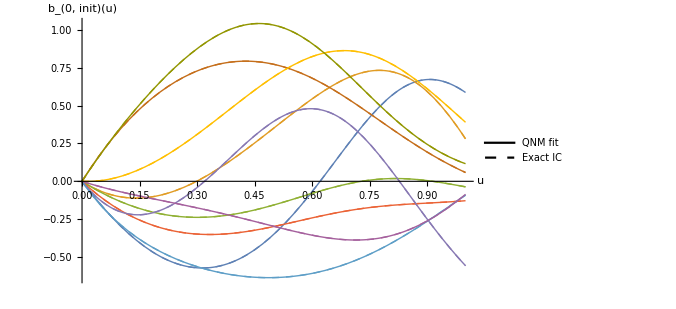

```mathematica
QNMICFitVariousIC=Show[
Plot[Evaluate[Table[bForms[[bi]],{bi,BkgToShow}]],{u,0,1},AxesLabel->{Style["u",FontSize->18,Bold,Italic],Style["b_(0, init)(u)",FontSize->18,Bold,Italic]},PlotRange->All,ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->{{Thick,Dashed}},PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{Style["QNM fit",FontSize->16,Italic],Style["Exact IC",FontSize->16,Italic]}],{Scaled[{0.1,0.9}], {0, 0.5}}]],
Plot[Evaluate[Table[Sum[cRe[i]*Reb0[i][u]-cIm[i]*Imb0[i][u],{i,1,NoQNM}]/.QNMFit[bi],{bi,1,NBkgsPert}]],{u,0,1},AxesLabel->{Style["u",FontSize->18,Bold,Italic],Style["b_(0, init)(u)",FontSize->18,Bold,Italic]},PlotRange->All,ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->Thick]]
```

```mathematica
(*Export["QNMICFitVariousIC.pdf",QNMICFitVariousIC];*)
```

### Evolve in time the zeroth order

```mathematica
Do[
δpRelBkgSameT[bi]=Table[{Δt*(i-1)/π,δpRelBkg[bi][[i,2]]},{i,1,Length[BkgdbMultiple[bi]]}];
δpRelFullSameT[bi]=Table[{Δt*(i-1)/π,δpRelFull[bi][[i,2]]},{i,1,Length[BkgdbMultiple[bi]]}];
,{bi,1,NBkgsPert}];
```

#### The approximate form for b

```mathematica
Do[
Δp0Approx[bi][t_]=-12*Re[Sum[Exp[Imω0[i]*t]*(cRe[i]+ⅈ*cIm[i])*(ReDb0[i]+ⅈ*ImDb0[i])*(Cos[Reω0[i]*t]-ⅈ*Sin[Reω0[i]*t]),{i,1,NoQNM}]]/.QNMFit[bi];
,{bi,1,NBkgsPert}]
```

#### Plot

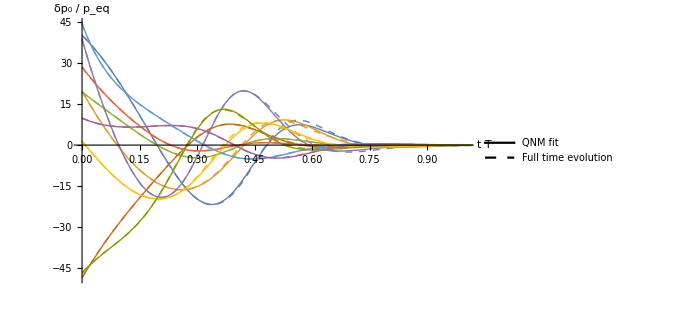

```mathematica
PressureBkgPlotNew=ListPlot[Table[δpRelBkgSameT[bi],{bi,1,NBkgsPert}],Joined->True,AxesLabel->{Style["t T",FontSize->18,Bold,Italic],Style["δp_0 / p_eq",FontSize->18,Bold,Italic]},PlotRange->{{0,1},All},ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->{{Dashed,Thick}}];
PressureApproxPlot=Plot[Evaluate[Table[Δp0Approx[bi][t*π],{bi,1,NBkgsPert}]],{t,0,1},AxesLabel->{Style["t T",FontSize->18,Bold,Italic],Style["δp / p_eq",FontSize->18,Bold,Italic]},PlotRange->All,ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->Thick,PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{Style["QNM fit",FontSize->16,Italic],Style["Full time evolution",FontSize->16,Italic]}],{Scaled[{0.55,0.9}], {0, 0.5}}]];
QNMZerothFitVariousIC=Show[PressureBkgPlotNew,PressureApproxPlot]
```

```mathematica
(*Export["QNMZerothFitVariousIC.pdf",QNMZerothFitVariousIC];*)
```

### Fit the δC_i

```mathematica
uMin=0;
uMax=1;
NumPoints=70;
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
uj=(uMin+(uMax-uMin)/2(1+xj));
xRule=Solve[uSym==uMin+(uMax-uMin)/2(1+xSym),xSym][[1]];
```

```mathematica
Do[
δQNMData=Table[Join[
Table[Reb0[i][uj[[j]]],{i,1,NoQNM}],
Table[Imb0[i][uj[[j]]],{i,1,NoQNM}],
{Sum[cRe[i]*ReδbInt[i][uj[[j]]]-cIm[i]*ImδbInt[i][uj[[j]]],{i,1,NoQNM}]/.QNMFit[bi]},{0}]
,{j,1,NumPoints+1}];

δQNMFit[bi]=FindFit[
δQNMData,
Sum[δcRe[i]*b0Re[i]-δcIm[i]*b0Im[i],{i,1,NoQNM}]+Intercept,
Join[Table[δcRe[i],{i,1,NoQNM}],Table[δcIm[i],{i,1,NoQNM}]],
Join[Table[b0Re[i],{i,1,NoQNM}],Table[b0Im[i],{i,1,NoQNM}],{Intercept}]];

δTableForPlot[bi]=Table[{uj[[j]],
(Sum[δcRe[i]*Reb0[i][uj[[j]]]-δcIm[i]*Imb0[i][uj[[j]]],{i,1,NoQNM}]/.δQNMFit[bi])+
(Sum[cRe[i]*ReδbInt[i][uj[[j]]]-cIm[i]*ImδbInt[i][uj[[j]]],{i,1,NoQNM}]/.QNMFit[bi])},{j,1,NumPoints+1}];

,{bi,1,NBkgsPert}]
```

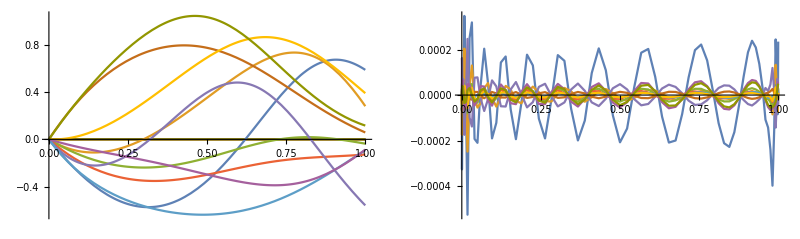

```mathematica
AbsPlot=ListPlot[Table[δTableForPlot[bi],{bi,1,NBkgsPert}],Joined->True,PlotRange->All];
RelPlot=Show[
ListPlot[Table[δTableForPlot[bi],{bi,1,NBkgsPert}],Joined->True,PlotRange->All],
Plot[Evaluate[Table[bForms[[bi]],{bi,1,NBkgsPert}]],{u,0,1},PlotRange->All],PlotRange->All];
GraphicsGrid[{{RelPlot,AbsPlot}},ImageSize->800]
```

### Evolve the perturbations in time

#### First, find the coefficients

#### Construct the approximate changes in pressure anisotropy

```mathematica
Do[
δΔpApprox[bi][t_]=-12*Re[Sum[Exp[Imω0[iQNM]*t]*(Cos[Reω0[iQNM]*t]-ⅈ*Sin[Reω0[iQNM]*t])*((δcRe[iQNM]+ⅈ*δcIm[iQNM])*(ReDb0[iQNM]+ⅈ*ImDb0[iQNM])+
(Reδdb[iQNM]+ⅈ*Imδdb[iQNM])*(cRe[iQNM]+ⅈ*cIm[iQNM])+1/2*(cRe[iQNM]+ⅈ*cIm[iQNM])*(ReDb0[iQNM]+ⅈ*ImDb0[iQNM])-ⅈ*t*(Reδω[iQNM]+ⅈ*Imδω[iQNM])*(cRe[iQNM]+ⅈ*cIm[iQNM])*(ReDb0[iQNM]+ⅈ*ImDb0[iQNM])),{iQNM,1,NoQNM}]]/.QNMFit[bi]/.δQNMFit[bi];
,{bi,1,NBkgsPert}]
```

#### By definition, pressure anisotropy is proportional to (check that there are no other factors of λGB flying around)

```mathematica
δpHatted=(1/2 τabValues[[4,4]]-1/2(1/2 τabValues[[2,2]]+1/2 τabValues[[3,3]]))/.τSol//Simplify
```

(3 (1-2 lcSym^2) b[4][t])/lcSym^5

#### Expand it in λGB

```mathematica
δpHattedSeries=Series[(δpHatted/.lcSym->lc/.b[4][t]->b0[4][t]+λGB*δb4[t]),{λGB,0,1}]
```

-3 b0[4][t]+(-3 δb4[t]-3/2 b0[4][t]) λGB+O[λGB]^2

```mathematica
ΔδpHatted=4D[Normal[δpHattedSeries],λGB]
```

4 (-3 δb4[t]-3/2 b0[4][t])

```mathematica
uMin=0;
uMax=1;
NumPoints=25;
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
uj=(uMin+(uMax-uMin)/2(1+xj));
xRule=Solve[uSym==uMin+(uMax-uMin)/2(1+xSym),xSym][[1]];
```

```mathematica
Do[
ΔδpHattedList[bi]={};
Do[
dbAtBoundaryLocal=BkgdbMultiple[bi][[i]][[NumPoints+1]];
δbValLoc=δbImport[bi][[i]];
δbLocRules=Table[δbj[j][t]->δbValLoc[[j]],{j,1,NumPoints+1}];
dδbAtBoundaryLocal=dδbVec[[NumPoints+1]]/.δbLocRules;
ΔδpHattedList[bi]=Append[ΔδpHattedList[bi],{Δt*(i-1)/π,ΔδpHatted/.δb4[t]->dδbAtBoundaryLocal/.b0[4][t]->dbAtBoundaryLocal}];
,{i,1,Length[BkgdbMultiple[bi]]}]
,{bi,1,NBkgsPert}]
```

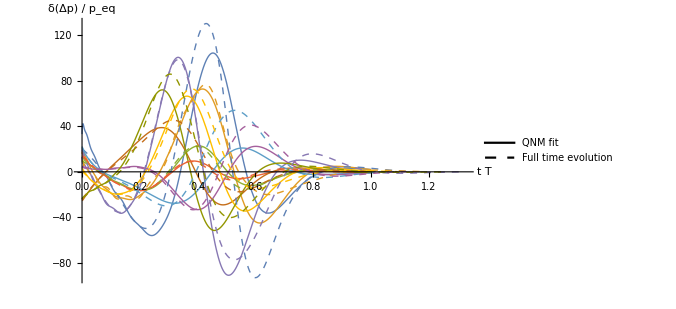

```mathematica
δΔpApproxPlot=Plot[Evaluate[Table[δΔpApprox[bi][t*π],{bi,1,NBkgsPert}]],{t,0,1},PlotRange->{All,All},PlotStyle->Thick,AxesLabel->{Style["t T",FontSize->18,Bold,Italic],Style["δ(Δp) / p_eq",FontSize->18,Bold,Italic]},ImageSize->500,LabelStyle->Directive[Black,14],PlotRange->All];
δΔpExactPlot=ListPlot[Table[ΔδpHattedList[bi],{bi,1,NBkgsPert}],Joined->True,PlotStyle->{{Dashed,Thick}},PlotRange->{{0,1},All},AxesLabel->{Style["t T",FontSize->18,Bold,Italic],Style["δ(Δp) / p_eq",FontSize->18,Bold,Italic]},ImageSize->500,LabelStyle->Directive[Black,14],PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{Style["QNM fit",FontSize->16,Italic],Style["Full time evolution",FontSize->16,Italic]}],{Scaled[{0.55,0.9}], {0, 0.5}}],PlotRange->All];
DeltaDeltaPlotVariousIC=Show[δΔpApproxPlot,δΔpExactPlot]
```

### Nice plots

```mathematica
Dynamic[bi]
Do[
ICPlotPretty[bi]=Plot[Sum[cRe[i]*Reb0[i][u]-cIm[i]*Imb0[i][u],{i,1,NoQNM}]/.QNMFit[bi],{u,0,1},
PlotStyle->{Thick,Black},AxesLabel->{"u","b_(0, init)(u)"},PlotRange->{{0,1},{-1,1}}],{bi,1,NBkgsPert}]
```

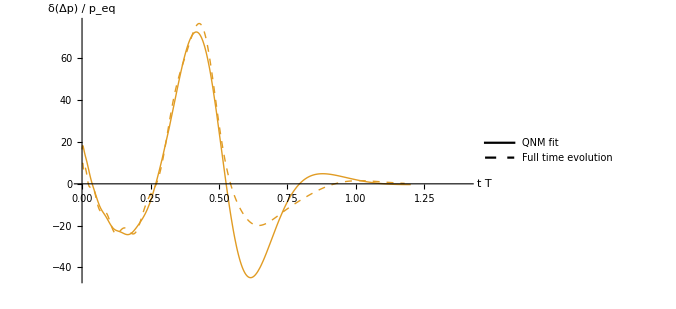

```mathematica
Do[
QNMCompPlot[bi]=Show[
Plot[δΔpApprox[bi][t*π],{t,0,1.2},PlotRange->All,PlotStyle->{ColorData[97,"ColorList"][[bi]],Thick},AxesLabel->{Style["t T",FontSize->18,Bold,Italic],Style["δ(Δp) / p_eq",FontSize->18,Bold,Italic]},ImageSize->500,LabelStyle->Directive[Black,14],
Epilog->{Inset[ICPlotPretty[bi],Scaled[{0.75,0.2}],Automatic,Scaled[0.4]]}],
ListPlot[ΔδpHattedList[bi],Joined->True,PlotStyle->{{Dashed,Thick,ColorData[97,"ColorList"][[bi]]}},ImageSize->500,LabelStyle->Directive[Black,14],PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{Style["QNM fit",FontSize->16,Italic],Style["Full time evolution",FontSize->16,Italic]}],{Scaled[{0.55,0.9}], {0, 0.5}}],PlotRange->All],PlotRange->{{0,1.4},All}
];
,{bi,1,NBkgsPert}]
QNMCompPlot[2]
```

```mathematica
Do[Export["QNM"<>ToString[bi]<>".pdf",QNMCompPlot[bi]],{bi,1,NBkgsPert}]
```

```mathematica
Manipulate[QNMCompPlot[bi],{bi,1,NBkgsPert,1}]
```

## Diagnostic plots

### Monitor progress

```mathematica
Dynamic[LogString]
```

### Compute the plot data

#### Get values of uH

```mathematica
LogString="Loading values of uH...";
uHValues=Table[Get["BkgData/Bkg-"<>BkgIdsPert[[bi]]<>".dat"][[3]],{bi,1,NBkgsPert}];
```

#### Get values of coefficients in QNM fits as lists

```mathematica
Do[
C0List[bi]=Table[{cRe[i],cIm[i]},{i,1,NoQNM}]/.QNMFit[bi];
δCList[bi]=Table[{δcRe[i],δcIm[i]},{i,1,NoQNM}]/.δQNMFit[bi];
,{bi,1,NBkgsPert}];
```

#### Compute the numerical δbNum for all the backgrounds

```mathematica
OldLogString=LogString<>"\nCalculating δbNum... ";
uMin=0;
uMax=1;
NumPoints=25;
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
uj=(uMin+(uMax-uMin)/2(1+xj));
xRule=Solve[uSym==uMin+(uMax-uMin)/2(1+xSym),xSym][[1]];
fTemp[u_]=Sum[α[n]*ChebyshevT[n-1,xSym/.xRule],{n,1,NumPoints+1}]/.uSym->u;
Do[
LogString=OldLogString<>"Bkg. "<>ToString[bi]<>" / "<>ToString[NBkgsPert];
Do[
δbCoeffs[bi][t]=Solve[Table[fTemp[uj[[j]]]==δbImport[bi][[t]][[j]],{j,1,NumPoints+1}],Table[α[n],{n,1,NumPoints+1}]][[1]];
δbNum[bi][t][u_]=fTemp[u]/.δbCoeffs[bi][t];
,{t,1,Length[δbImport[bi]]}]
,{bi,1,NBkgsPert}]
```

#### Interpolate all the QNM modes and define the interpolated δbQNM

```mathematica
uMin=0;
uMax=1;
NumPoints=100;
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
uj=(uMin+(uMax-uMin)/2(1+xj));
xRule=Solve[uSym==uMin+(uMax-uMin)/2(1+xSym),xSym][[1]];
```

```mathematica
OldLogString=LogString<>"\nInterpolating QNM mode functions... ";
Do[
LogString=OldLogString<>"QNM "<>ToString[iQNM]<>" / "<>ToString[NoQNM];
IntReb0[iQNM]=Interpolation[Table[{u,Reb0[iQNM][u]},{u,uj}]];
IntImb0[iQNM]=Interpolation[Table[{u,Imb0[iQNM][u]},{u,uj}]];
IntReδbInt[iQNM]=Interpolation[Table[{u,ReδbInt[iQNM][u]},{u,uj}]];
IntImδbInt[iQNM]=Interpolation[Table[{u,ImδbInt[iQNM][u]},{u,uj}]];
,{iQNM,1,NoQNM}]
```

```mathematica
Do[
δbQNMInt[bi][t_,u_]=Re[Sum[Exp[Imω0[iQNM]*(t-1)*Δt]*(Cos[Reω0[iQNM]*(t-1)*Δt]-ⅈ*Sin[Reω0[iQNM]*(t-1)*Δt])*((δcRe[iQNM]+ⅈ*δcIm[iQNM])*(IntReb0[iQNM][u]+ⅈ*IntImb0[iQNM][u])+
(IntReδbInt[iQNM][u]+ⅈ*IntImδbInt[iQNM][u])*(cRe[iQNM]+ⅈ*cIm[iQNM])-ⅈ*(t-1)*Δt*(Reδω[iQNM]+ⅈ*Imδω[iQNM])*(cRe[iQNM]+ⅈ*cIm[iQNM])*(IntReb0[iQNM][u]+ⅈ*IntImb0[iQNM][u])),{iQNM,1,NoQNM}]]/.QNMFit[bi]/.δQNMFit[bi];
,{bi,1,NBkgsPert}]
```

#### The longest: compute differences in b_0

```mathematica
OldLogString=LogString<>"\nCalculating differences in b0:\n";
Do[
DiffList[bi]={};
MaxδbList[bi]={};
MaxDiffList[bi]={};
Do[
LogString=OldLogString<>"Bkg "<>ToString[bi]<>" / "<>ToString[NBkgsPert]<>", t = "<>ToString[t]<>" / "<>ToString[Length[δbImport[bi]]];
TempList=Table[{u,Abs[δbQNMInt[bi][t,u]-δbNum[bi][t][u]]},{u,uj}];
AbsDiffInt=Interpolation[TempList];
MaxDiffList[bi]=Append[MaxDiffList[bi],{(t-1)*Δt*1/π,Max[TempList[[;;,2]]]}];
DiffList[bi]=Append[DiffList[bi],{(t-1)*Δt*1/π,NIntegrate[AbsDiffInt[u],{u,0,1}]}];
MaxδbList[bi]=Append[MaxδbList[bi],{(t-1)*Δt*1/π,Max[Table[Abs[δbNum[bi][t][u]],{u,uj}]]}];
,{t,1,Length[δbImport[bi]]}]
,{bi,1,NBkgsPert}]
```

### Set plotting parameters

#### Set the plot labels

```mathematica
ICLabels=Table["Random IC # "<>ToString[i]<>", second batch",{i,1,NBkgsPert}];
```

#### Set the x-axis limits for plotting

```mathematica
tMaxPert=1.4;
tMaxBkg=1.2;
MyUMax=Table[1,{i,1,NBkgsPert}];
```

### Generate plots and export

```mathematica
OldLogString=LogString<>"\nGenerating plots: ";
Do[
LogString=OldLogString<>"Bkg "<>ToString[bi]<>" / "<>ToString[NBkgsPert];
(* Main panel *)
MainPanel[bi]=Show[
Plot[δΔpApprox[bi][t*π],{t,0,tMaxPert},PlotRange->All,PlotStyle->{ColorData[97,"ColorList"][[bi]],Thick},AxesLabel->{Style["t T",FontSize->18,Bold,Italic],Style["δ(Δp) / p_eq",FontSize->18,Bold,Italic]},ImageSize->700,LabelStyle->Directive[Black,14]],
ListPlot[ΔδpHattedList[bi],Joined->True,PlotStyle->{{Dashed,Thick,ColorData[97,"ColorList"][[bi]]}},ImageSize->700,LabelStyle->Directive[Black,14],PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{Style["QNM fit",FontSize->16,Italic],Style["Full time evolution",FontSize->16,Italic]}],{Scaled[{0.55,0.9}], {0, 0.5}}],PlotRange->All],PlotRange->{{0,tMaxPert},All},PlotLabel->Style[ICLabels[[bi]],FontSize->16,Italic]
,AspectRatio->0.7];
(* Upper left sidepanel *)
SidePanelUL[bi]=Plot[Sum[cRe[i]*Reb0[i][u]-cIm[i]*Imb0[i][u],{i,1,NoQNM}]/.QNMFit[bi],{u,0,MyUMax[[bi]]},
PlotStyle->{Thick,Black},PlotRange->{{0,1},{-1,1}},AxesLabel->{Style["u",FontSize->14,Bold,Italic],Style["b_(0, init)(u)",FontSize->14,Bold,Italic]},ImageSize->300,LabelStyle->Directive[Black,12],AspectRatio->0.7];
(* Upper right sidepanel *)
SidePanelUR[bi]=Show[
ListPlot[δpRelBkgSameT[bi],Joined->True,AxesLabel->{Style["t T",FontSize->14,Bold,Italic],Style["δp_0 / p_eq",FontSize->14,Bold,Italic]},PlotRange->All,ImageSize->300,LabelStyle->Directive[Black,12],PlotStyle->{Dashed,Thick,ColorData[97,"ColorList"][[bi]]}],
Plot[Δp0Approx[bi][t*π],{t,0,tMaxBkg},AxesLabel->{Style["t T",FontSize->14,Bold,Italic],Style["δp_0 / p_eq",FontSize->14,Bold,Italic]},PlotRange->All,ImageSize->300,LabelStyle->Directive[Black,12],PlotStyle->{Thick,ColorData[97,"ColorList"][[bi]]},PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{Style["QNM fit",FontSize->12,Italic],Style["Full time evolution",FontSize->12,Italic]}],{Scaled[{0.4,0.1}], {0, 0.5}}]],
PlotRange->{{0,tMaxBkg},All},PlotLabel->Style["u_H = "<>ToString[NumberForm[uHValues[[bi]],3]],FontSize->12],AspectRatio->0.7];
(* Lower left sidepanels *)
SidePanelLL1[bi]=BarChart[C0List[bi],AxesOrigin->{0,0},ChartLabels->{Table[Style[ToString[i],Bold,Black,FontSize->14],{i,1,NoQNM}],None},LabelStyle->Directive[Black,14](*,ChartLegends->{"ReC_i^(0)","ImC_i^(0)"}*),ImageSize->300,AspectRatio->0.35];
SidePanelLL2[bi]=BarChart[δCList[bi],AxesOrigin->{0,0},ChartLabels->{Table[Style[ToString[i],Bold,Black,FontSize->14],{i,1,NoQNM}],None},LabelStyle->Directive[Black,14],(*ChartLegends->{"ReδC_i","ImδC_i"},*)ImageSize->300,AspectRatio->0.35];
(* Lower right sidepanel *)
SidePanelLR[bi]=ListPlot[{MaxDiffList[bi],DiffList[bi],MaxδbList[bi]},Joined->True,AxesLabel->{Style["t T",FontSize->12,Bold,Italic],None},PlotRange->All,ImageSize->300,LabelStyle->Directive[Black,12],PlotStyle->{{Thick},{Thick},{Thick,Black,Dashed}},PlotLegends->Placed[{Style["max(|(b^(0))_num - (b^(0))_QNM)",FontSize->10,Italic],Style["∫du |(b^(0))_num - (b^(0))_QNM|",FontSize->10,Italic],Style["max(|(b^(0))_num|)",FontSize->10,Italic]},{Scaled[{0.3,0.8}], {0, 0.5}}],AspectRatio->0.7];
(* Assemble them together *)
SidePanelLL[bi]=GraphicsGrid[{{SidePanelLL1[bi]},{SidePanelLL2[bi]}}];
SidePanel[bi]=GraphicsGrid[{{SidePanelUL[bi],SidePanelUR[bi]},{SidePanelLL[bi],SidePanelLR[bi]}},Spacings->{0.5,0.5}];
FullPlot[bi]=GraphicsGrid[{{MainPanel[bi],SidePanel[bi]}}];
,{bi,1,NBkgsPert}]
```

### Inspect and export

```mathematica
LogString=LogString<>"\nExporting...";
Do[
Export["FullPlot"<>ToString[bi]<>".pdf",FullPlot[bi]];
,{bi,1,NBkgsPert}]
LogString=LogString<>"\nDone!";
```